```mathematica
(*It is very strange how it appears that Nc = 20 gives virtually the same results as Nc=100; the results dont seem very impressed by the Nc value;*)
```

```mathematica
Clear["`*"];
plotfigs=0;
simType=2;
sims={1,12};
{simi,nsim}={1,21};
garbage=0;gcor=0;
esence=Range[sims[[2]]-sims[[1]]+1];
Monitor[For[Simulation=sims⟦1⟧,Simulation≤sims⟦2⟧,Simulation++,Clear[vars,pars,varset,folder,zeros,nvarset,pars,names,safeNames,values,pars,X,Y,Z,q1,q2,q3,Vp,μ,data,H,Q1,Q2,VT,V0,LTT,L0T,LT0,L00,Xallin,Xallout,Yallin,Yallout,Hallout,q1allout,q2allout,Pc,ck1,ck2,ck3,kx,ky,kz,kperp,w,ph,Vcorff,VcorTT,noactparticles,VcorTN,VcorNT,t0,tc,tt,tmax,Nt,Nreal,Nc,Nloop,Np,ntraj,Nci,Nce,Ti,Te,Zeff,Aeff,ndens,vth,rhoi,wi,Ln,Li,Le,magneticmodel,B0,R0,a0,s1,s2,s3,q00,r00,psi0,amp,elong,device,shot,shotslice,NgridR,NgridZ,Omgt0,Omgtprim,turbmodel,xcorr,ycorr,tcorr,Phi,turbprof,Ai,Ae,lambdax,lambday,lambdaz,lbalonz,tauc,k0i,k0e,gammaZF,gammaE,X0,Y0,Z0,Ts,Es,pitch,As,Zs,taucc,positiontype,pitchtype,energytype,USElarmor,USEcoll,USEturb,USEmagnturb,USEfreq,USEpolar,USEPC,USEreal,USEcorr,USEballoon,USEtilt,USEtesting,C1,C2,C3];If[simType==1,folder=StringDrop[NotebookDirectory[],-12]<>"data/Sim_";];If[simType==2,folder=StringDrop[NotebookDirectory[],-12]<>"data/DB_";];If[Simulation<10,folder=folder<>"0"<>ToString[Simulation]<>"/";,folder=folder<>ToString[Simulation]<>"/";];expfoto=StringTake[folder,StringLength[folder]-15]<>"Arxiv/";nsim2=nsim-simi+1;varset={wevary,pars,X,Y,Z,q1,q2,q3,Vp,μ,data,H,Q1,Q2,VT,V0,LTT,L0T,LT0,L00,Xallin,Xallout,Yallin,Yallout,Hallout,q1allout,q2allout,Pc,ck1,ck2,ck3,kx,ky,kz,kperp,w,ph,Vcorff,VcorTT,noactparticles,VcorTN,VcorNT};nvarset=Length[varset];zeros=Table[0,{i,nvarset},{j,nsim2}];MapThread[Set,{varset,zeros}];varset=ConstantArray[Range[nsim2],Length[varset]];For[i=simi,i≤nsim,i++,run="Run_"<>StringJoin[Table["0",{i,4-IntegerPart[Log[10.,i]]}]];igood=i-simi+1;dd=Flatten[Import[folder<>run<>ToString[i]<>"/file_01.dat","Table"]];If[simType==1,{pars⟦igood⟧=dd⟦Position[dd,"exported"]⟦1,1⟧+3;;Length[dd]⟧;info=dd⟦1;;Position[dd,"exported"]⟦1,1⟧+3⟧;wevary⟦igood⟧=StringReplace[StringSplit[info⟦8⟧,"("]⟦1⟧,"_"->""];};];If[simType==2,{dd=Flatten[Import[folder<>run<>ToString[i]<>"/file_01.dat","Table"]];pars⟦igood⟧=dd⟦Position[dd,"t0"]⟦1,1⟧;;Length[dd]⟧;pzpz=Flatten[Position[dd⟦1;;Position[dd,"t0"]⟦1,1⟧⟧,"|"]]⟦3;;4⟧;de=StringRiffle[Rest[Most[dd⟦1;;Position[dd,"t0"]⟦1,1⟧⟧⟦pzpz⟦1⟧;;pzpz⟦2⟧⟧]]];wevary⟦igood⟧=StringReplace[First[StringCases[de,"selection=Vary_ "~~x:(Except["\""]..)~~"_only":>x]],"_"->""];};];len=IntegerPart[1/2 Length[pars⟦igood⟧]];{names,values}={pars⟦igood,1;;len⟧,pars⟦igood,len+1;;2 len⟧};safeNames=StringReplace[names,"_"->""];vars=Symbol/@safeNames;MapThread[Set,{vars,values}];{Nreal,Nc,Np,Nt,Nloop,ntraj}=Rationalize[{Nreal,Nc,Np,Nt,Nloop,ntraj}];noactparticles⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_24.bin","Real64"],{Nreal,Nloop}];If[garbage==1,{X⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_02.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Y⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_03.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Z⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_04.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Vp⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_05.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];μ⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_06.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];H⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_07.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];q1⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_08.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];q2⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_09.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];q3⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_10.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Pc⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_25.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];ck1⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_26.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];ck2⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_27.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];ck3⟦igood⟧=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_28.bin","Real64"],{Nreal,Nloop,ntraj,Nt+1}];Xallin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_13.bin","Real64"];Yallin⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_14.bin","Real64"];Xallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_15.bin","Real64"];Yallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_16.bin","Real64"];Hallout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_17.bin","Real64"];q1allout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_18.bin","Real64"];q2allout⟦igood⟧=BinaryReadList[folder<>run<>ToString[i]<>"/file_19.bin","Real64"];}];If[gcor==1,Vcorff⟦igood⟧=Mean[Mean[ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_20.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]]];VcorTT⟦igood⟧=Mean[Mean[ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_21.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]]];VcorTN⟦igood⟧=Mean[Mean[ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_22.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]]];VcorNT⟦igood⟧=Mean[Mean[ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_23.bin","Real64"],{Nreal,Nloop,Nt+1,Nt+1}]]];];VcorNN=Vcorff-VcorTT-VcorNT-VcorTN;dar=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_11.bin","Real64"],{Nreal,Nloop,Nt+1,4}];{Q1⟦igood⟧,VT⟦igood⟧,V0⟦igood⟧,LT0⟦igood⟧}=Table[dar⟦All,All,All,is⟧,{is,4}];dar=ArrayReshape[BinaryReadList[folder<>run<>ToString[i]<>"/file_12.bin","Real64"],{Nreal,Nloop,Nt+1,4}];{Q2⟦igood⟧,LTT⟦igood⟧,L0T⟦igood⟧,L00⟦igood⟧}=Table[dar⟦All,All,All,is⟧,{is,4}];Clear@@safeNames;];dt=tmax/Nt;ρ=√((X-1.)^2+Y^2);z=Y;x=X Cos[Z];y=X Sin[Z];Thread[Evaluate[ToExpression[vars]]=Transpose[pars⟦All,1+len;;2 len⟧]];aver[dtt_,pas_]:=Table[GaussianFilter[Mean[Mean[noactparticles⟦as⟧ dtt⟦as⟧]],pas]/Np⟦as⟧,{as,nsim2}];speed1[dtt_,τ_]:=Table[Transpose[{τ⟦as⟧,(rhoi⟦as⟧ (RotateLeft[dtt⟦as⟧]-RotateRight[dtt⟦as⟧]))/((R0⟦as⟧ (2 τ⟦as,2⟧))/vth⟦as⟧)}],{as,nsim2}];difuz1[dtt2_,dtt1_,τ_]:=Table[Transpose[{τ⟦as⟧,(rhoi⟦as⟧^2 (RotateLeft[dtt2⟦as⟧-dtt1⟦as⟧^2]-RotateRight[dtt2⟦as⟧-dtt1⟦as⟧^2]))/((R0⟦as⟧ (4 τ⟦as,2⟧))/vth⟦as⟧)}],{as,nsim2}];speed2[dtt_,τ_]:=Table[Transpose[{τ⟦as⟧,(rhoi⟦as⟧ (dtt⟦as⟧-dtt⟦as,1⟧))/((R0⟦as⟧ (τ⟦as⟧+1/10^9))/vth⟦as⟧)}],{as,nsim2}];difuz2[dtt2_,dtt1_,τ_]:=Table[Transpose[{τ⟦as⟧,(rhoi⟦as⟧^2 (dtt2⟦as⟧-dtt1⟦as⟧^2-(dtt2⟦as,1⟧-dtt1⟦as,1⟧^2)))/((R0⟦as⟧ (2 τ⟦as⟧+1/10^9))/vth⟦as⟧)}],{as,nsim2}];pas=1;t=Table[dt⟦as⟧ (Range[Nt⟦as⟧+1]-1),{as,Length[Q1]}];{𝓆1,𝓆2,π1,π2,𝒽1,𝒽2,𝓋t1,𝓋t2}={aver[Q1,pas],aver[Q2,pas],aver[VT,pas],aver[LTT,pas],aver[V0,pas],aver[L0T,pas],aver[LT0,pas],aver[L00,pas]};{VQ1,DQ1,VQ2,DQ2,Vπ1,Dπ1,Vπ2,Dπ2,V𝒽1,D𝒽1,V𝒽2,D𝒽2,V𝒯1,D𝒯1,V𝒯2,D𝒯2}={speed1[𝓆1,t],difuz1[𝓆2,𝓆1,t],speed2[𝓆1,t],difuz2[𝓆2,𝓆1,t],speed1[π1,t],difuz1[π2,π1,t],speed2[π1,t],difuz2[π2,π1,t],speed1[𝒽1,t],difuz1[𝒽2,𝒽1,t],speed2[𝒽1,t],difuz2[𝒽2,𝒽1,t],speed1[𝓋t1,t],difuz1[𝓋t2,𝓋t1,t],speed2[𝓋t1,t],difuz2[𝓋t2,𝓋t1,t]};DQ1⟦All,1,2⟧=DQ1⟦All,2,2⟧ 0;For[i=1,i≤nsim2,i++,DQ1⟦i,Nt⟦i⟧+1,2⟧=DQ1⟦i,Nt⟦i⟧,2⟧;];VQ1⟦All,1,2⟧=VQ1⟦All,2,2⟧;shear=(2 r00^2 s3)/(a0^2 s1+r00^2 s3);ϵ0=8.85/10^12;logL=17.;e=1.6/10^19;mi=1.6/10^27;nub0=(4.0 logL ndens ((Zeff Zs e^2)/(ϵ0 mi As))^2 (√(Aeff/2.0))^3)/((8.0 π) vth^3);nub=((4.0 logL ndens ((Zeff Zs e^2)/(ϵ0 mi As))^2 (√(Aeff/2.0))^3) ((r00 R0) q00 √2))/(((8.0 π) vth^3) (vth √r00));frac=0.7;frac2=0.95;VQas=Table[Mean[VQ1⟦i,IntegerPart[frac Nt⟦i⟧];;IntegerPart[Nt⟦i⟧-1],2⟧],{i,nsim2}];DQas=Table[Mean[DQ1⟦i,IntegerPart[frac Nt⟦i⟧];;IntegerPart[Nt⟦i⟧-1],2⟧],{i,nsim2}];VQas2=Table[Mean[VQ2⟦i,IntegerPart[frac2 Nt⟦i⟧];;IntegerPart[Nt⟦i⟧-1],2⟧],{i,nsim2}];DQas2=Table[Mean[DQ2⟦i,IntegerPart[frac2 Nt⟦i⟧];;IntegerPart[Nt⟦i⟧-1],2⟧],{i,nsim2}];Γgyro=(rhoi/(a0 R0))^2 vth As;esence[[Simulation]]={wevary⟦1⟧,ToExpression[wevary⟦1⟧],VQas,DQas};If[plotfigs==1,{pozvar=len+{19,15,32,34,26,27,42,44,46,47,48,50,53,63,66}⟦Simulation⟧;pozvar=len+{49,66,21,47,63,67,58,51,52,53,54,55}⟦Simulation⟧;cine=names⟦pozvar-len⟧;cat=pars⟦All,pozvar⟧;fig1={ListPlot[Transpose[{cat,VQas}],PlotTheme->"Scientific",FrameLabel->{cine,"V[\!\(\*SuperscriptBox[\(m\), \(2\)]\)/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotMarkers->Automatic,PlotRange->All],ListPlot[Transpose[{cat,DQas}],PlotTheme->"Scientific",FrameLabel->{cine,"D[\!\(\*SuperscriptBox[\(m\), \(2\)]\)/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotMarkers->Automatic,PlotRange->All]};fig2={ListPlot[VQ1,PlotTheme->"Scientific",FrameLabel->{"t[R0/\!\(\*SubscriptBox[\(v\), \(th\)]\)]","V[\!\(\*SuperscriptBox[\(m\), \(2\)]\)/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotRange->Automatic],ListPlot[DQ1,PlotTheme->"Scientific",FrameLabel->{"t[R0/\!\(\*SubscriptBox[\(v\), \(th\)]\)]","D[\!\(\*SuperscriptBox[\(m\), \(2\)]\)/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotRange->All]};nmax=Min[10^4,Np⟦1⟧];fig3=Table[ListPlot[{Transpose[{Xallout⟦as,1;;nmax⟧,Yallout⟦as,1;;nmax⟧}],Transpose[{Xallin⟦as,1;;nmax⟧,Yallin⟦as,1;;nmax⟧}]},PlotRange->All,PlotStyle->{Red,Blue}],{as,nsim2}];Export[folder<>"fig_1_a.png",fig1⟦1⟧];Export[folder<>"fig_1_b.png",fig1⟦2⟧];Export[folder<>"fig_2_a.png",fig2⟦1⟧];Export[folder<>"fig_2_b.png",fig2⟦2⟧];If[garbage==1,For[as=1,as≤nsim2,as++,Export[folder<>"fig_3_"<>ToString[as]<>".png",fig3⟦as⟧]];];}];],{Row[{ProgressIndicator[i,{1,nsim2}],ToString[i]<>"/"<>ToString[nsim2]}],Row[{ProgressIndicator[Simulation,{sims⟦1⟧,sims⟦2⟧}],ToString[Simulation]<>"/"<>ToString[sims⟦2⟧-sims⟦1⟧]}]}];
```

Set::setraw: Cannot assign to raw object Ai.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

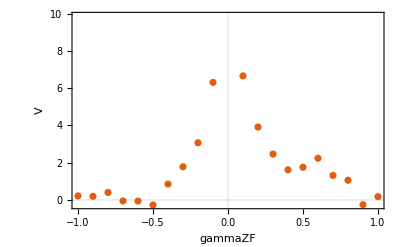
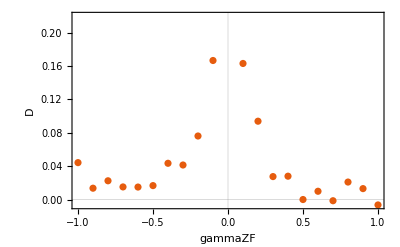

```mathematica
i=7;{ListPlot[{Transpose[{esence⟦i,2⟧,esence⟦i,3⟧}]},PlotTheme->"Scientific",FrameLabel->{esence[[i,1]],"V"}],ListPlot[{Transpose[{esence⟦i,2⟧,esence⟦i,4⟧}]},PlotTheme->"Scientific",FrameLabel->{esence[[i,1]],"D"}]}
```

```mathematica
fsa={"Ai","As","Ln","Phi","Ts","Zs","gamma_ZF","lambdax","lambday","lambdaz","lbalonz","tauc"};
Table[Position[pars[[1,1;;len]],fsa[[i]] ],{i,Length[fsa]}]//Flatten
```

{49,66,21,47,63,67,58,51,52,53,54,55}

```mathematica
{turbmodel,ycorr,xcorr}//Transpose//MatrixForm
```

(2. | 1. | 2.
2. | 1. | 2.
2. | 1. | 2.
2. | 1. | 2.
2. | 1. | 2.
2. | 1. | 2.
2. | 1. | 2.
2. | 1. | 2.
2. | 1. | 2.
2. | 1. | 2.
2. | 1. | 2.)

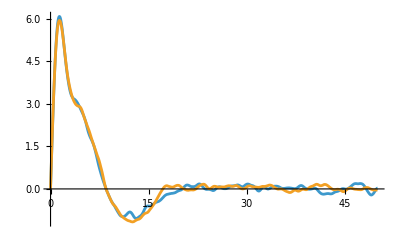

```mathematica
ListLinePlot[{DQ1⟦2⟧,DQ1⟦4⟧},PlotRange->All]
```

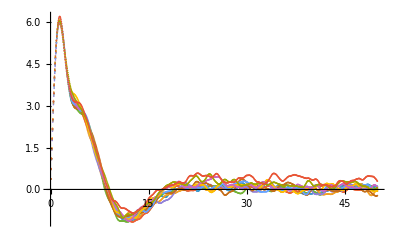

```mathematica
ListPlot[DQ1,PlotRange->All]
```

```mathematica
DQas
```

{0.016625,-0.00733653,0.0288625,0.00471079,0.00409586,0.00798893,0.0426645,0.0408178,0.080994,0.154689,0.337774}

```mathematica
pars[[1,-len+Flatten[Position[HeavisideTheta[Abs[pars⟦1⟧-pars⟦2⟧]-1/10^7],1]]]]
```

{Ln}

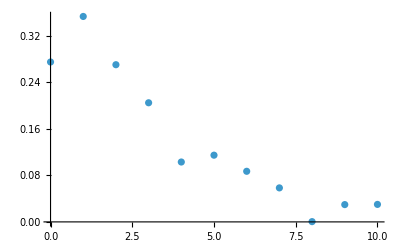

```mathematica
{Ln,DQas}//Transpose//ListPlot
```

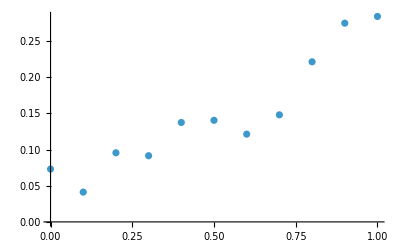

```mathematica
{Ai,DQas}//Transpose//ListPlot
```

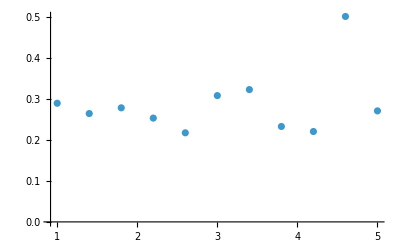

```mathematica
{As,DQas}//Transpose//ListPlot
```

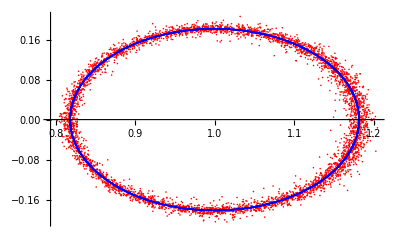

```mathematica
as=9;nmax=5 10^3;ListPlot[{Transpose[{Xallout⟦as,1;;nmax⟧,Yallout⟦as,1;;nmax⟧}],Transpose[{Xallin⟦as,1;;nmax⟧,Yallin⟦as,1;;nmax⟧}]},PlotRange->All,PlotStyle->{Red,Blue}]
```

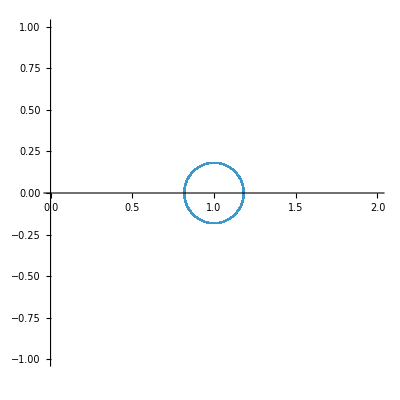
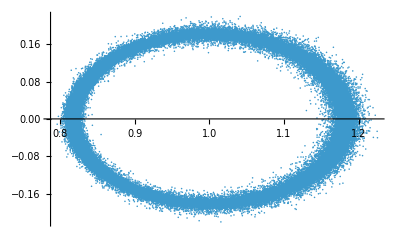

{0,0,1.2176}

```mathematica
as=1;nmax=Np⟦1⟧;
{ListPlot[Transpose[{Xallin⟦as,1;;nmax⟧,Yallin⟦as,1;;nmax⟧}],AspectRatio->1,PlotRange->{{0,2},{-1,1}}],ListPlot[Transpose[{Flatten[Xallout⟦as,1;;nmax⟧],Flatten[Yallout⟦as,1;;nmax⟧]}],PlotRange->All]}
{Count[Flatten[kz],Indeterminate],kperp//Max,X//Max}
```

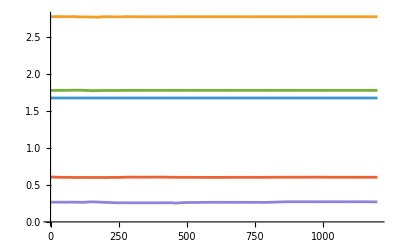
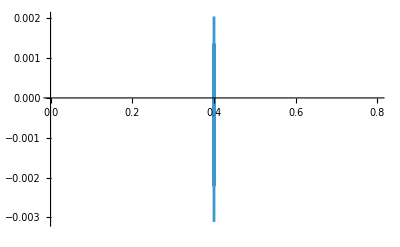

```mathematica
as=3;{ListLinePlot[Table[(H⟦as,1,1,o⟧),{o,5}]],ListLinePlot[Table[{pitch[[as]],Table[Mean[(H⟦as,1,1,o⟧/H⟦as,1,1,o,1⟧-1) 100],{o,1,5}]⟦1⟧},{as,nsim2}],PlotRange->All]}
```

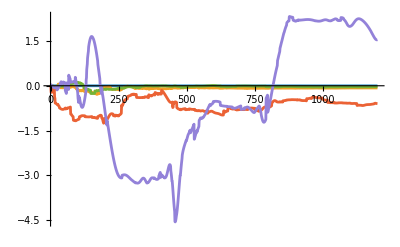
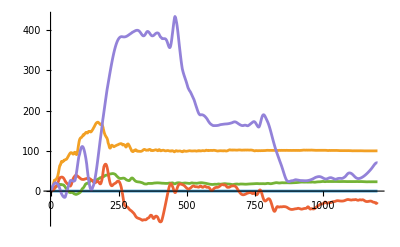

```mathematica
as=3;{ListLinePlot[Table[(H⟦as,1,1,o⟧/H⟦as,1,1,o,1⟧-1) 10^2,{o,5}],PlotRange->All],ListLinePlot[Table[(Pc⟦as,1,1,o⟧/Pc⟦as,1,1,o,1⟧-1) 10^4,{o,5}],PlotRange->All]}
```

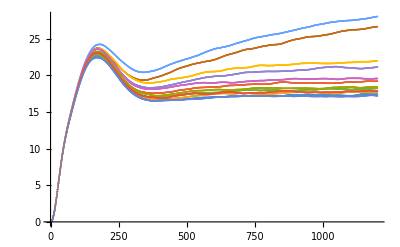
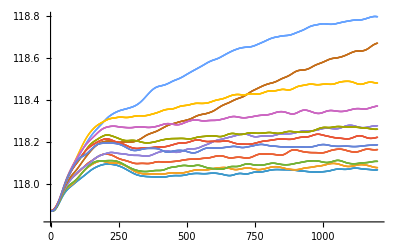

```mathematica
{ListPlot[𝓆2-𝓆1^2,PlotRange->All,ImageSize->400],ListPlot[𝓆1,PlotRange->All,ImageSize->400]}
```

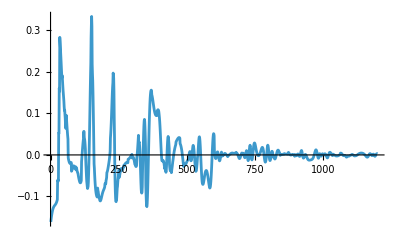

```mathematica
ListLinePlot[ck1⟦1,1,1,2⟧,PlotRange->All]
```

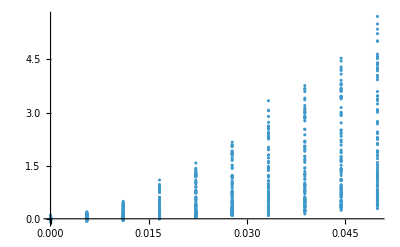

```mathematica
ListPlot[Sort[Transpose[{Phi,DQas}]],PlotRange->All]
```

```mathematica
ListPointPlot3D[Sort[Transpose[{Ai,Phi,DQas}]],PlotRange->All]
```

-Graphics3D-

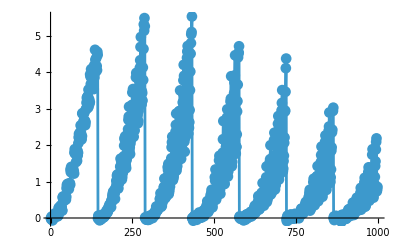
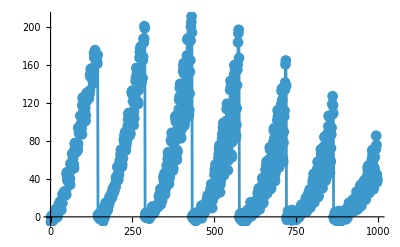

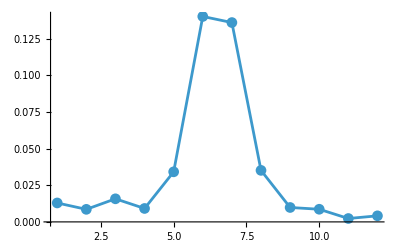
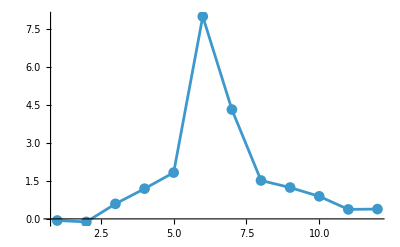

```mathematica
{ListPlot[DQas,PlotRange->All,Joined->True,PlotMarkers->Automatic],ListPlot[VQas,PlotRange->All,Joined->True,PlotMarkers->Automatic]}
```

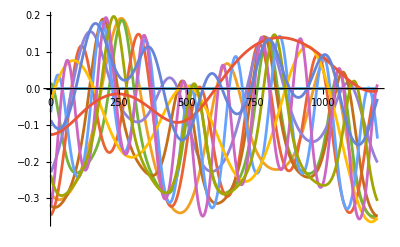

```mathematica
ListLinePlot[Table[X[[o,1,1,1]]-X[[1,1,1,1]],{o,nsim2}],PlotRange->All]
```

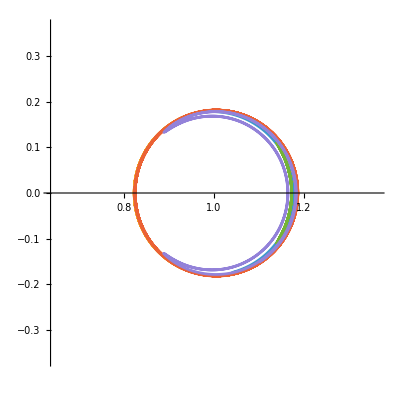

```mathematica
as=1;da=1;
ListLinePlot[Table[Transpose[{X⟦as,1,da,sa⟧-0Mean[X⟦as,1,da,sa⟧],Y⟦as,1,da,sa⟧-0Mean[Y⟦as,1,da,sa⟧]}],{sa,ntraj[[1]]/2}],PlotRange->{{1-a0[[1]],1+a0[[1]]},{-a0[[1]],a0[[1]]}},AspectRatio->1]
```

```mathematica
QQ1=ArrayReshape[q1,{nsim2 Nreal[[1]]Nloop[[1]]ntraj[[1]]//IntegerPart,Nt[[1]]+1//IntegerPart}];
QQ2=ArrayReshape[q2,{nsim2 Nreal[[1]]Nloop[[1]]ntraj[[1]]//IntegerPart,Nt[[1]]+1//IntegerPart}];
```

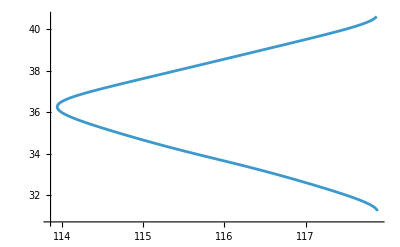

```mathematica
ListLinePlot[Table[Transpose[{QQ1⟦as⟧,QQ2⟦as⟧}],{as,1,1}],PlotRange->Automatic]
```

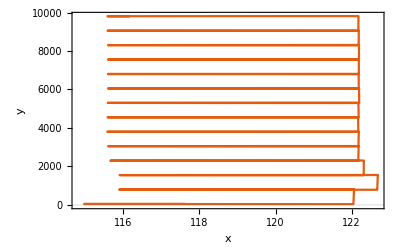
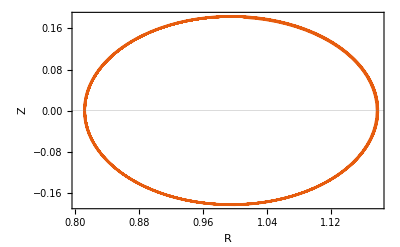
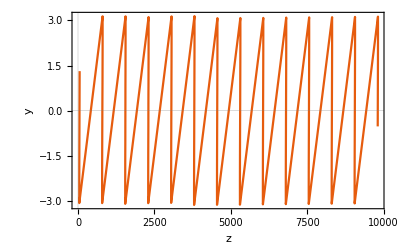

```mathematica
whc=2;os=3;
{ListLinePlot[Transpose[{q1⟦os,1,1,whc⟧,q2⟦os,1,1,whc⟧}],PlotRange->All,FrameLabel->{"x","y"},PlotTheme->"Scientific"],ListLinePlot[Transpose[{X⟦os,1,1,whc⟧,Y⟦os,1,1,whc⟧}],PlotRange->All,FrameLabel->{"R","Z"},PlotTheme->"Scientific"],ListLinePlot[Transpose[{q2⟦os,1,1,whc⟧,q3⟦os,1,1,whc⟧}],PlotRange->All,FrameLabel->{"z","y"},PlotTheme->"Scientific"]}
```

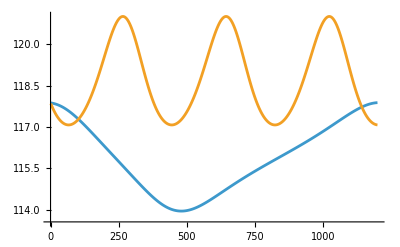
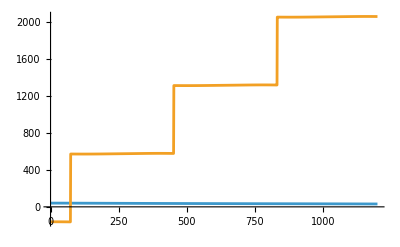
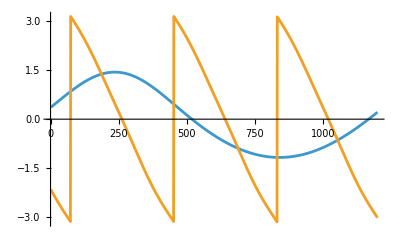

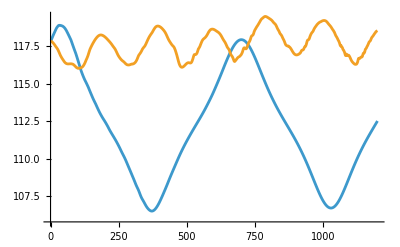
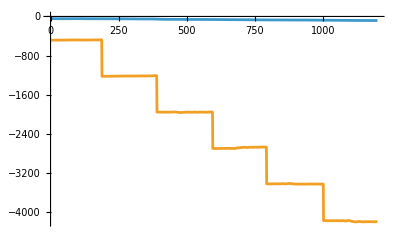
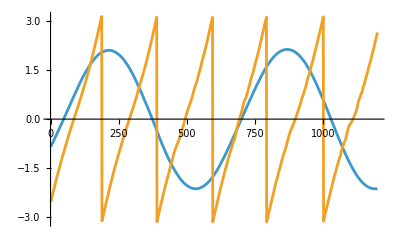

```mathematica
as1=1;as2=2;whc=5;
{ListLinePlot[{q1⟦as1,1,1,1⟧,q1⟦as2,1,1,1⟧}],ListLinePlot[{q2⟦as1,1,1,1⟧,-q2⟦as2,1,1,1⟧}],ListLinePlot[{q3⟦as1,1,1,1⟧,-q3⟦as2,1,1,1⟧}]}
{ListLinePlot[{q1⟦as1,1,1,whc⟧,q1⟦as2,1,1,whc⟧}],ListLinePlot[{q2⟦as1,1,1,whc⟧,-q2⟦as2,1,1,whc⟧}],ListLinePlot[{q3⟦as1,1,1,whc⟧,-q3⟦as2,1,1,whc⟧}]}
```

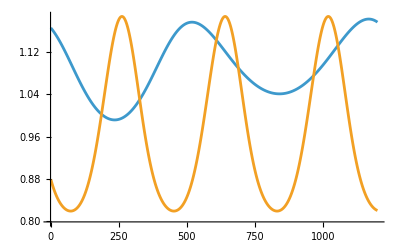
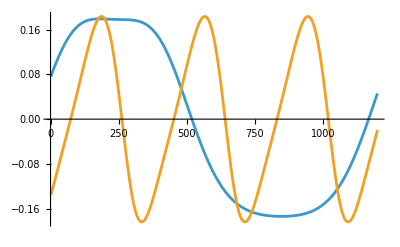
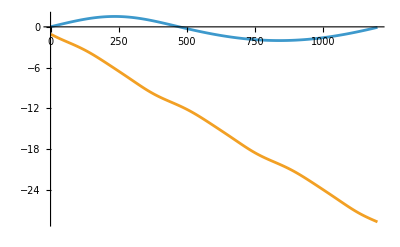
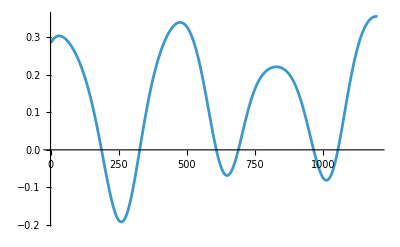
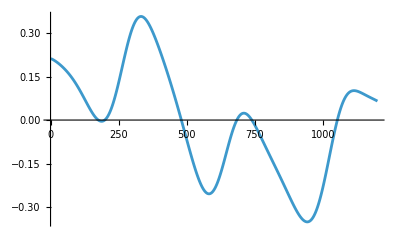
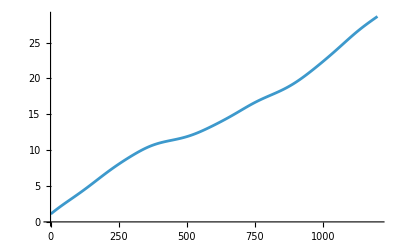

```mathematica
{ListLinePlot[{X⟦as1,1,1,1⟧,X⟦as2,1,1,1⟧}],ListLinePlot[{Y⟦as1,1,1,1⟧,-Y⟦as2,1,1,1⟧}],ListLinePlot[{Z⟦as1,1,1,1⟧,-Z⟦as2,1,1,1⟧}],ListLinePlot[X⟦as1,1,1,1⟧-X⟦as2,1,1,1⟧],ListLinePlot[Y⟦as1,1,1,1⟧+Y⟦as2,1,1,1⟧],ListLinePlot[Z⟦as1,1,1,1⟧+Z⟦as2,1,1,1⟧]}
```

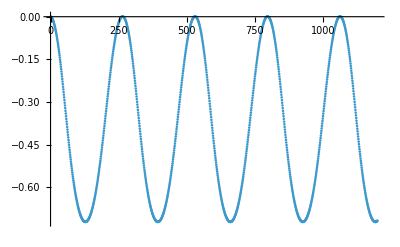

```mathematica
Vp[[3,1,1,1]]/Vp[[3,1,1,1,1]]-1//ListPlot
```

```mathematica
gradB={{(B0^2 (a0^4 R0 r00^2+(1+r00) (R0-R0 r00) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2+(a0^4 R0 (a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) (-1+X0) X0)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3))))/((a0^4 (-safe1^2+r00^2 (-1+safe1^2))+2 a0^3 r00 (-1+r00^2) safe1 safe2+2 a0 r00^3 (-1+r00^2) safe2 safe3+r00^4 (-1+r00^2) safe3^2+a0^2 r00^2 (-1+r00^2) (safe2^2+2 safe1 safe3)) X0),(a0^4 B0^2 R0 (a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) Y0)/((-1+r00) (1+r00) (a0^2 safe1+a0 r00 safe2+r00^2 safe3) (a0^4 (-safe1^2+r00^2 (-1+safe1^2))+2 a0^3 r00 (-1+r00^2) safe1 safe2+2 a0 r00^3 (-1+r00^2) safe2 safe3+r00^4 (-1+r00^2) safe3^2+a0^2 r00^2 (-1+r00^2) (safe2^2+2 safe1 safe3)))},{-((a0^4 B0^2 R0 (a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) Y0)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3) (a0^4 (-safe1^2+r00^2 (-1+safe1^2))+2 a0^3 r00 (-1+r00^2) safe1 safe2+2 a0 r00^3 (-1+r00^2) safe2 safe3+r00^4 (-1+r00^2) safe3^2+a0^2 r00^2 (-1+r00^2) (safe2^2+2 safe1 safe3)) √((1-(a0^4 r00^2)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2))/X0^2) X0)),-(B0^2 R0 (1-(a0^4 (-1+X0)^2)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2)-(a0^4 (a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) (-1+X0) X0)/((-1+r00^2)^2 (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^3)-(a0^4 Y0^2)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2)))/(((1-(a0^4 r00^2)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2))/X0^2)^(3/2) X0^4),-((a0^2 B0^2 (a0^4 (2 safe1^2-r00^2 (-1+safe1^2))-a0^3 r00 (-3+r00^2) safe1 safe2+a0 r00^3 (1+r00^2) safe2 safe3+r00^6 safe3^2+a0^2 r00^2 (safe2^2+2 safe1 safe3)))/(√(1-r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3) (a0^4 (-safe1^2+r00^2 (-1+safe1^2))+2 a0^3 r00 (-1+r00^2) safe1 safe2+2 a0 r00^3 (-1+r00^2) safe2 safe3+r00^4 (-1+r00^2) safe3^2+a0^2 r00^2 (-1+r00^2) (safe2^2+2 safe1 safe3)) √((1-(a0^4 r00^2)/((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2))/X0^2) X0^2))}};
```

```mathematica
{gradB,rotB}={gradB⟦1⟧,gradB⟦2⟧};
```

```mathematica
{psir,psiz,psirr,psirz,psizz}={(a0^2 R0 (-1+X0))/(√(-R0^2 (-1+r00^2)) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)),(a0^2 R0 Y0)/(√(-R0^2 (-1+r00^2)) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)),-(a0^2 R0^2 (-((a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) (-1+X0)^2)+(-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3) Y0^2))/((-R0^2 (-1+r00^2))^(3/2) (a0 r00 (a0 safe1+r00 safe2)+r00^3 safe3)^2),(a0^2 R0^2 (a0^2 r00 safe1+a0 (-1+2 r00^2) safe2+r00 (-2+3 r00^2) safe3) (-1+X0) Y0)/(r00 (-R0^2 (-1+r00^2))^(3/2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3)^2),-(a0^2 R0^2 ((-1+r00^2) (a0^2 safe1+a0 r00 safe2+r00^2 safe3) (-1+X0)^2-(a0^2 safe1+a0 r00^3 safe2+r00^2 (-1+2 r00^2) safe3) Y0^2))/((-R0^2 (-1+r00^2))^(3/2) (a0 r00 (a0 safe1+r00 safe2)+r00^3 safe3)^2)};
```

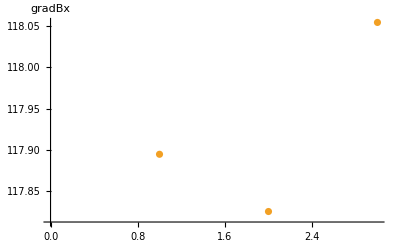
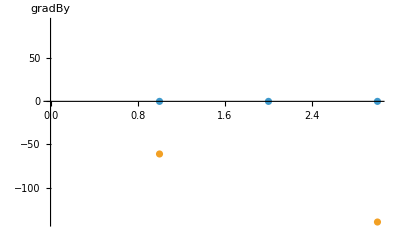
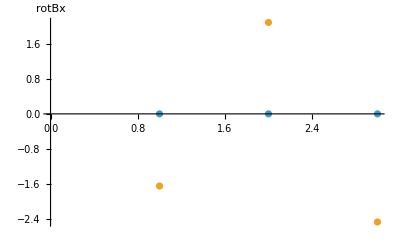
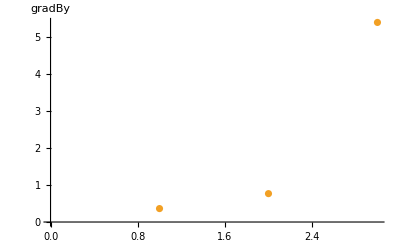

```mathematica
{ListPlot[{gradB⟦1⟧,q1⟦All,1,1,1,1⟧},AxesLabel->{"","gradBx"}],ListPlot[{gradB⟦2⟧,q2⟦All,1,1,1,1⟧},AxesLabel->{"","gradBy"}],ListPlot[{rotB⟦1⟧,q3⟦All,1,1,1,1⟧},AxesLabel->{"","rotBx"}],ListPlot[{rotB⟦2⟧,H⟦All,1,1,1,1⟧},AxesLabel->{"","gradBy"}]}
```

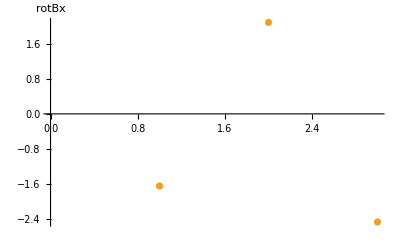
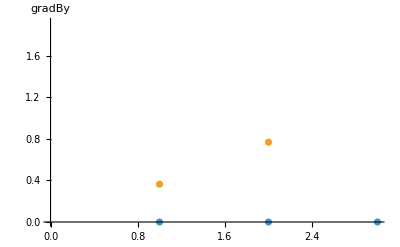

```mathematica
{ListPlot[{psir R0,q3⟦All,1,1,1,1⟧},AxesLabel->{"","rotBx"}],ListPlot[{R0 psiz,H⟦All,1,1,1,1⟧},AxesLabel->{"","gradBy"}]}
```

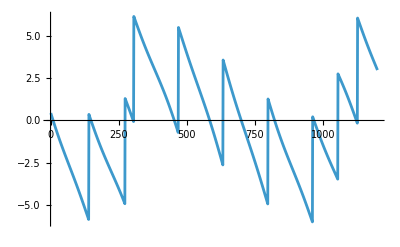

```mathematica
ListLinePlot[q3⟦as1,1,1,1⟧+q3⟦as2,1,1,1⟧]
```

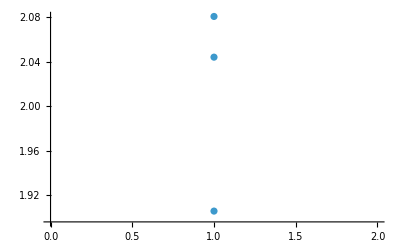

```mathematica
ListPlot[{lambdaz,DQas}//Transpose,PlotRange->All]
```

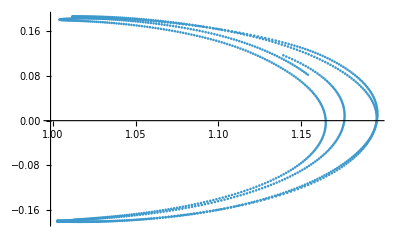
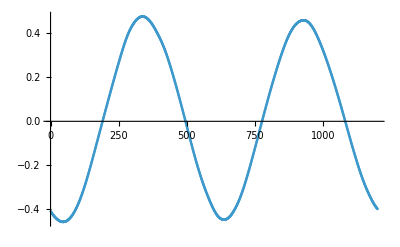
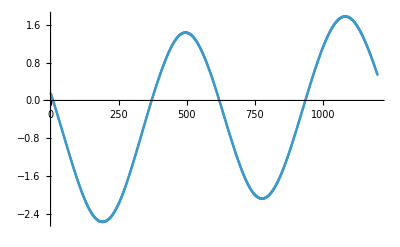
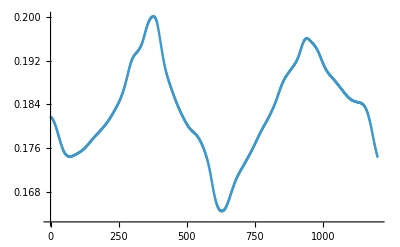

```mathematica
max=Nt[[1]];sa=4;da=1;{ListPlot[Transpose[{X⟦1,1,da,sa,1;;max⟧,Y⟦1,1,da,sa,1;;max⟧}]],ListPlot[Vp⟦1,1,da,sa,1;;max⟧],ListPlot[Z⟦1,1,da,sa,1;;max⟧],ListPlot[ρ⟦1,1,da,sa,1;;max⟧]}
```

```mathematica
Monitor[For[i=1,i≤nsim2,i++,For[j=1,j≤Nloop⟦i⟧,j++,Subscript[trajx, i,j]=Interpolation[Transpose[{t⟦i⟧,x⟦i,1,j,2⟧}]];Subscript[trajy, i,j]=Interpolation[Transpose[{t⟦i⟧,y⟦i,1,j,2⟧}]];Subscript[trajz, i,j]=Interpolation[Transpose[{t⟦i⟧,z⟦i,1,j,2⟧}]];]],{i,j}]
```

```mathematica
torus[u_,v_,R_:1,r_:a0⟦1⟧]:={(R+r Cos[v]) Cos[u],(R+r Cos[v]) Sin[u],r Sin[v]};
limits={{-(1+a0⟦1⟧),1+a0⟦1⟧},{-(1+a0⟦1⟧),1+a0⟦1⟧},{-a0⟦1⟧,a0⟦1⟧}};
torusSurface=ParametricPlot3D[torus[u,v],{u,0,3π/2},{v,0,2π},Mesh->None,PlotStyle->Directive[Opacity[0.4],ColorFunction->"TemperatureMap",Specularity[White,50]],Lighting->"Neutral",ColorFunctionScaling->True];
{i,j}={1,3};
colors={{Red},{Blue},{Green},{Orange},{Pink},{Magenta},{Cyan},{Black},{Brown},{Gray}};
colors=Black;trajs=Table[{Subscript[trajx, i,j][τ],Subscript[trajy, i,j][τ],Subscript[trajz, i,j][τ]},{j,Nloop⟦1⟧}];trajs=ParametricPlot3D[{trajs⟦1⟧,trajs⟦2⟧,trajs⟦3⟧},{τ,0,14+0 tmax⟦1⟧},PlotRange->limits,PlotStyle->{Hue[0.58]}];
Show[trajs,torusSurface,Boxed->False,Axes->False,ImageSize->Large]
```

Part::partw: Part 3 of {{0.938982,0.450778,0.17653},{0.328572,-0.808367,0.129352}} does not exist.

Part::partw: Part 3 of {{1.08789,0.0745278,0.154994},{0.6157,-0.575548,0.0893572}} does not exist.

Part::partw: Part 3 of {{1.07993,-0.340448,0.119054},{0.784559,-0.255264,0.0437352}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of {{0.0706198,-0.919626,0.0211687}} does not exist.

Part::partw: Part 2 of {{-0.381717,-0.841233,0.000369373}} does not exist.

Part::partw: Part 2 of {{-0.7436,-0.557572,-0.0196391}} does not exist.

Part::partw: Part 2 of {{trajx_(2,1)[0.000286],trajy_(2,1)[0.000286],trajz_(2,1)[0.000286]}} does not exist.

Part::partw: Part 2 of {{trajx_(2,1)[0.286],trajy_(2,1)[0.286],trajz_(2,1)[0.286]}} does not exist.

Part::partw: Part 2 of {{trajx_(2,1)[0.571715],trajy_(2,1)[0.571715],trajz_(2,1)[0.571715]}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Monitor[For[i=1,i≤nsim2,i++,For[j=1,j≤Nloop⟦i⟧,j++,Subscript[trajx, i,j]=Interpolation[Transpose[{t⟦i⟧,X⟦i,1,j,2⟧}]];Subscript[trajy, i,j]=Interpolation[Transpose[{t⟦i⟧,Y⟦i,1,j,2⟧}]];]],{i,j}]
```

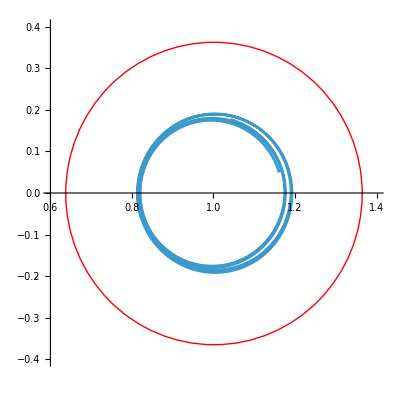

```mathematica
{i,j}={1,3};Show[ParametricPlot[Table[{Subscript[trajx, i,j][τ],Subscript[trajy, i,j][τ]},{j,Nloop⟦1⟧}],{τ,0,14+0 tmax⟦1⟧},PlotRange->{{0.6,1.4},{-.4,.4}}],Graphics[{Red,Circle[{1,0},a0⟦1⟧]}]]
```

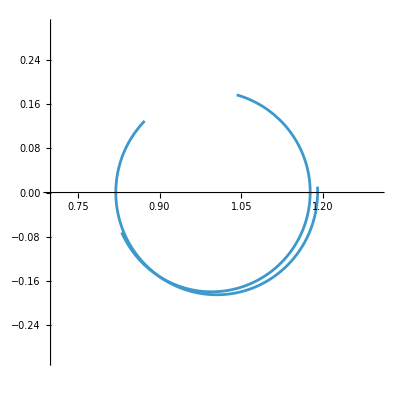

```mathematica
ParametricPlot[Table[{Subscript[trajx, i,j][τ],Subscript[trajy, i,j][τ]},{j,Nloop[[1]]}],{τ,0,4+0tmax[[1]]},PlotRange->{{0.7,1.3},{-.3,.3}}]
```

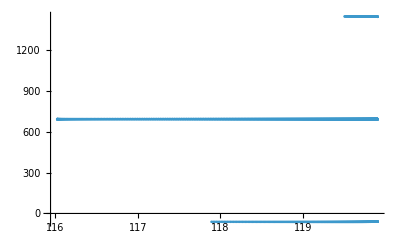
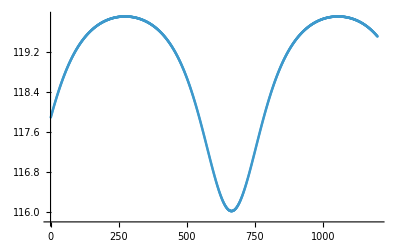
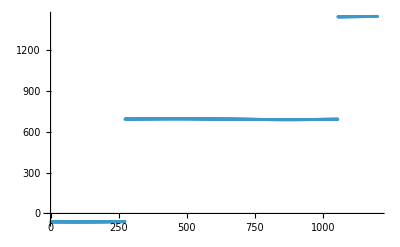
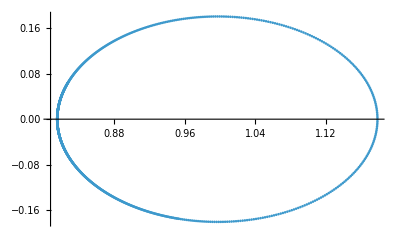

```mathematica
{{q1[[1,1,1,1]],q2[[1,1,1,1]]}//Transpose//ListPlot,q1[[1,1,1,1]]//ListPlot,q2[[1,1,1,1]]//ListPlot,{X[[1,1,1,1]],Y[[1,1,1,1]]}//Transpose//ListPlot}
```

```mathematica
Λ0=1/2 Table[HeavisideTheta[i-j-0.01]+HeavisideTheta[i-j+0.01],{i,Nt⟦1⟧+1},{j,Nt⟦1⟧+1}];Λ0⟦All,1⟧=1/2;Λ0⟦1,1⟧=0;
Λ=(R0⟦1⟧ dt⟦1⟧ Λ0)/vth⟦1⟧;
```

```mathematica
as=1;{kz[[as]],kperp[[as]]}//Transpose//ListPlot
as=9;{kz[[as]],kperp[[as]]}//Transpose//ListPlot
```

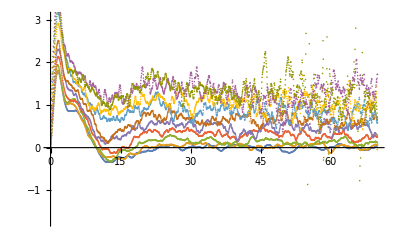

```mathematica
DQ1//ListPlot
```

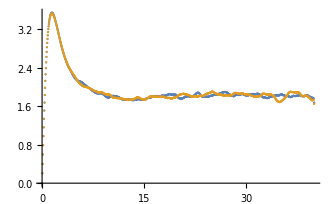

```mathematica
ListPlot[DQ1,PlotRange->All]
```

```mathematica
fact=1.0;neo=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,1,2}]/a0[[1]]/fact//Flatten;
coll=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,3,4}]/a0[[1]]/fact//Flatten;
turb=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,5,6}]/a0[[1]]/fact//Flatten;
full=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,7,8}]/a0[[1]]/fact//Flatten;
neo=neo-Mean[neo];
coll=coll-Mean[coll];
turb=turb-Mean[turb];
full=full-Mean[full];
```

Part::partw: Part 3 of {{0.139856,-0.14328,-0.187594,0.0245752,-0.166823,0.0874501,-0.181927,0.067053,-0.0836942,0.03165,-0.185014,0.138395,0.159406,-0.0537734,-0.0135886,-0.136251,-0.164288,-0.158686,«16»,-0.043998,-0.152344,0.0316431,-0.147691,0.0762724,0.064894,0.157854,0.196725,-0.157828,-0.00964634,-0.0831779,0.064175,0.191481,-0.163157,0.217674,-0.205034,«499950»},{«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

$Aborted

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of turb-Mean[turb].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of full-Mean[full].

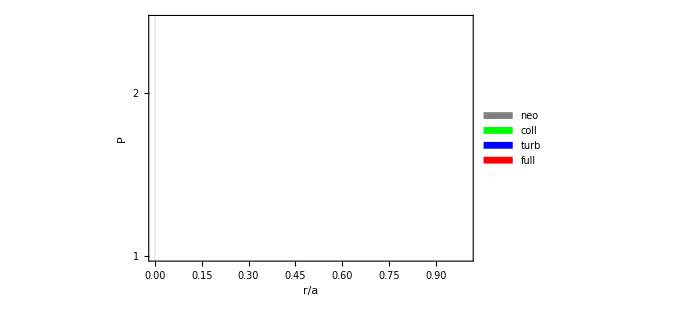

```mathematica
legend=Grid[{{Graphics[{Gray,Disk[{0,0},0.1]},ImageSize->15],Style["neo",15,FontFamily->"Times New Roman"]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["coll",15,FontFamily->"Times New Roman"]},{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["turb",15,FontFamily->"Times New Roman"]},{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["full",15,FontFamily->"Times New Roman"]}}];histo=Histogram[{neo,coll,turb,full},{0.01},PlotRange->All,ScalingFunctions->"Log",PlotTheme->"Scientific",LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,FrameLabel->{"r/a","P"},ChartStyle->{Gray,Green,Blue,Red},ChartLegends->Placed[legend,{0.8,0.8}]]
```

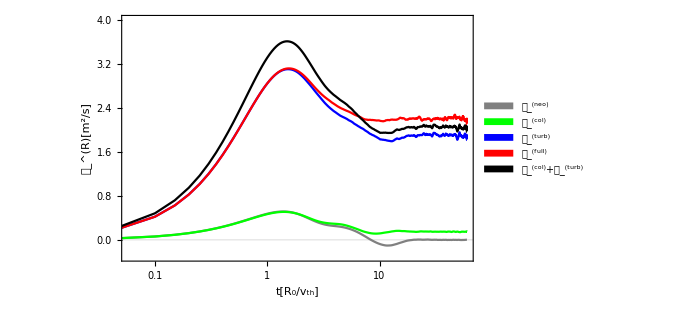

```mathematica
legend=Grid[{{Graphics[{Gray,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_^(neo)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_^(col)",FontFamily->"Times New Roman",15,Bold]},
{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_^(turb)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_^(full)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Black,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_^(col)+𝒟_^(turb)",FontFamily->"Times New Roman",15,Bold]}}];
timecomp=ListLogLinearPlot[{Mean[DQ1⟦1;;2⟧],Mean[DQ1⟦3;;4⟧],Mean[DQ1⟦5;;6⟧],Mean[DQ1⟦7;;8⟧],{Mean[DQ1⟦3;;4,All,1⟧],Mean[DQ1⟦3;;4,All,2⟧]+Mean[DQ1⟦5;;6,All,2⟧]}//Transpose},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},{-0.3,4}},PlotLegends->Placed[legend,{0.15,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Gray,Green,Blue,Red,Black},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

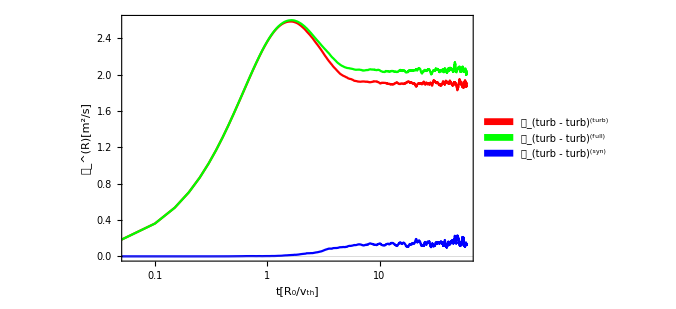

```mathematica
legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - turb)^(turb)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - turb)^(full)",FontFamily->"Times New Roman",15,Bold]},
{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - turb)^(syn)",FontFamily->"Times New Roman",15,Bold]}}];
i=1;timecomp=ListLogLinearPlot[{Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTT⟦5;;6⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTT⟦7;;8⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTT⟦7;;8⟧-VcorTT⟦5;;6⟧-VcorTT⟦3;;4⟧]]]}]},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},All},PlotLegends->Placed[legend,{0.15,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

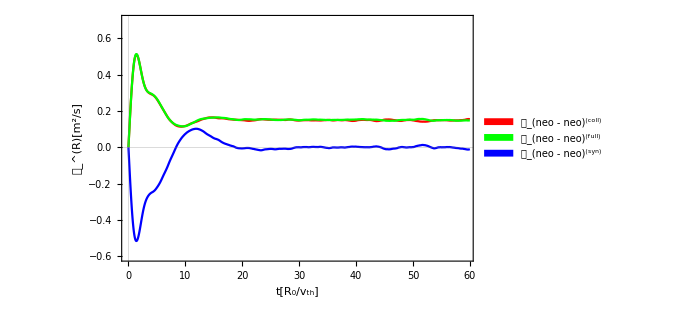

```mathematica
legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - neo)^(coll)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - neo)^(full)",FontFamily->"Times New Roman",15,Bold]},
{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - neo)^(syn)",FontFamily->"Times New Roman",15,Bold]}}];
i=1;timecomp=ListPlot[{Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦3;;4⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦7;;8⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦7;;8⟧-VcorNN⟦3;;4⟧-VcorNN⟦5;;6⟧]]]}]},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},{-0.6,0.7}},PlotLegends->Placed[legend,{0.2,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

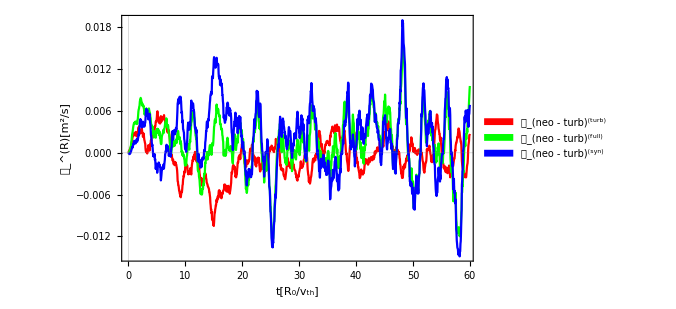

```mathematica
legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - turb)^(turb)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - turb)^(full)",FontFamily->"Times New Roman",15,Bold]},
{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(neo - turb)^(syn)",FontFamily->"Times New Roman",15,Bold]}}];
i=1;timecomp=ListPlot[{Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNT⟦5;;6⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNT⟦7;;8⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNT⟦7;;8⟧-VcorNT⟦5;;6⟧-VcorNT⟦3;;4⟧]]]}]},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},All},PlotLegends->Placed[legend,{0.15,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

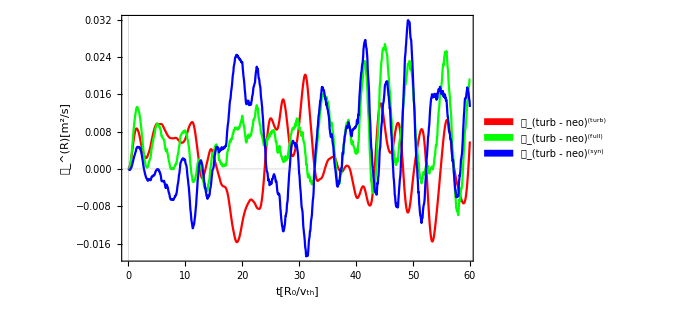

```mathematica
legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - neo)^(turb)",FontFamily->"Times New Roman",15,Bold]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - neo)^(full)",FontFamily->"Times New Roman",15,Bold]},
{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["𝒟_(turb - neo)^(syn)",FontFamily->"Times New Roman",15,Bold]}}];
i=1;timecomp=ListPlot[{Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTN⟦5;;6⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTN⟦7;;8⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorTN⟦7;;8⟧-VcorTN⟦5;;6⟧-VcorTN⟦3;;4⟧]]]}]},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},All},PlotLegends->Placed[legend,{0.15,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

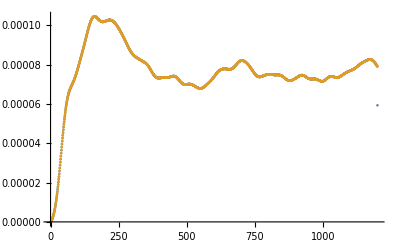
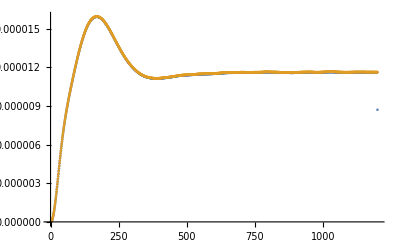

```mathematica
i=2;{ListPlot[{Λ.VQ1⟦i,All,2⟧,rhoi[[i]](𝓆1[[i]]-𝓆1[[i,1]])}],ListPlot[{Λ.DQ1[[i,All,2]],1/2 rhoi[[i]]^2(𝓆2[[i]]-𝓆1[[i]]^2)},PlotRange->All]}
```

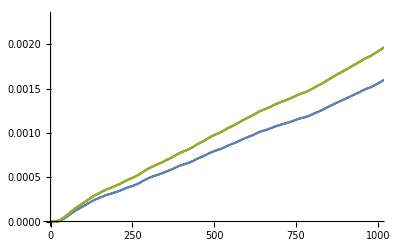
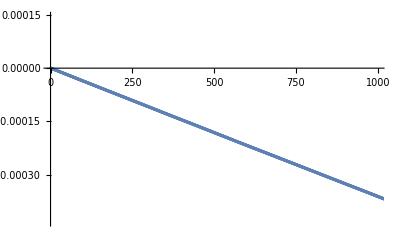

```mathematica
i=8;{ListPlot[{Λ.(vth⟦i⟧ Mean[Mean[VT⟦i⟧+V0⟦i⟧]]),Λ.VQ1⟦i,All,2⟧,rhoi⟦1⟧ (𝓆1⟦i⟧-𝓆1⟦i,1⟧)},PlotRange->{{0,999},Automatic}],ListPlot[{Λ.(vth⟦i⟧ Mean[Mean[VT⟦i⟧+V0⟦i⟧]])-Λ.VQ1⟦i,All,2⟧},PlotRange->{{0,999},Automatic}]}
```

```mathematica
i=2;ListLinePlot[{Λ.Mean[Mean[vth⟦i⟧ V0⟦i⟧]],Λ.Mean[Mean[vth⟦i⟧ VT⟦i⟧]],vth⟦i⟧ Λ.Mean[Mean[V0⟦i⟧+VT⟦i⟧]],rhoi⟦1⟧ (Mean[Mean[Q1⟦i⟧]]-Mean[Mean[Q1⟦i⟧]][[1]])},PlotStyle->{Red,Blue,Green,Orange},PlotLegends->Placed[{"Neo","Turb","full","real"},{1.,.6}],PlotRange->All,ImageSize->400]
```

-Graphics-

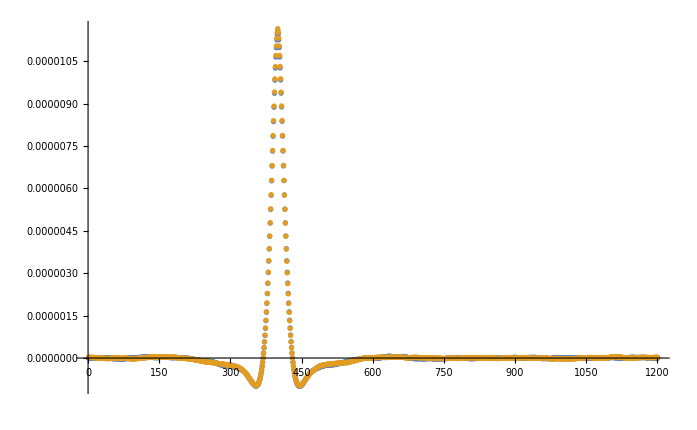
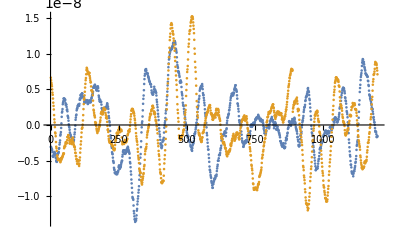
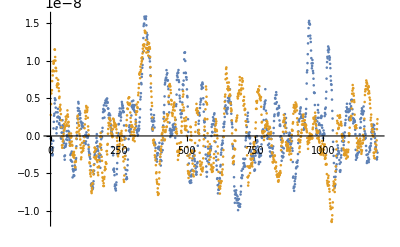
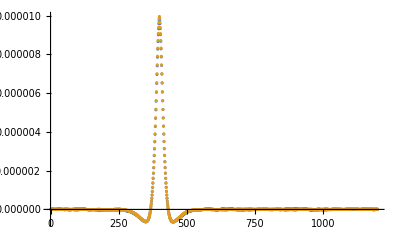
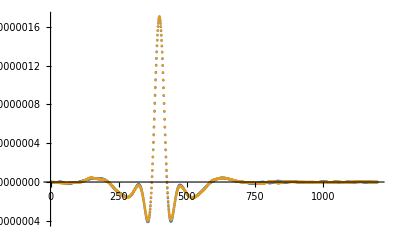

```mathematica
i=8;{t1,t2}={400,712};{ListPlot[{Vcorff⟦i,t1⟧,RotateLeft[Vcorff⟦i,t2⟧,-(t1-t2)]},PlotRange->All],ListPlot[{VcorNT⟦i,t1⟧,RotateLeft[VcorNT⟦i,t2⟧,-(t1-t2)]},PlotRange->All],ListPlot[{VcorTN⟦i,t1⟧,RotateLeft[VcorTN⟦i,t2⟧,-(t1-t2)]},PlotRange->All],ListPlot[{VcorTT⟦i,t1⟧,RotateLeft[VcorTT⟦i,t2⟧,-(t1-t2)]},PlotRange->All],ListPlot[{VcorNN⟦i,t1⟧,RotateLeft[VcorNN⟦i,t2⟧,-(t1-t2)]},PlotRange->All]}
```

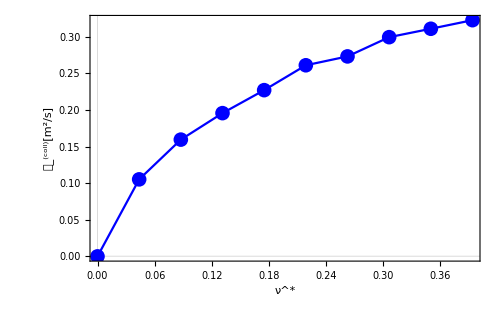

```mathematica
ListPlot[Transpose[{nub,DQas}],PlotTheme->"Scientific",PlotRange->All,ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["ν^*",FontFamily->"Times New Roman",Bold],Style["𝒟_^(coll)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True,PlotMarkers->{Automatic,15}]
```

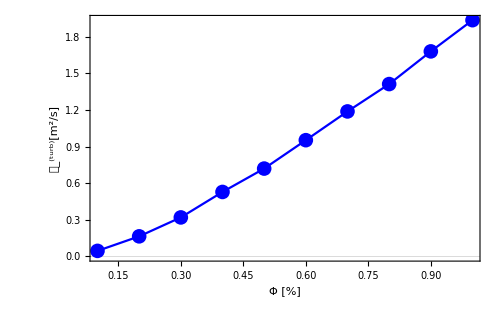

```mathematica
ListPlot[Transpose[{100Phi,DQas}],PlotTheme->"Scientific",PlotRange->All,ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["Φ [%]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(turb)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True,PlotMarkers->{Automatic,15}]
```

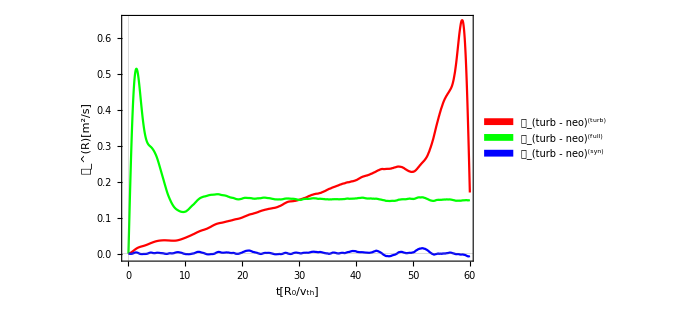

```mathematica
timecomp=ListPlot[{Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦i⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦7;;8⟧]]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Mean[VcorNN⟦7;;8⟧-VcorNN⟦3;;4⟧]]]}]},PlotTheme->"Scientific",PlotRange->{{0,0.99Max[t]},All},PlotLegends->Placed[legend,{0.15,0.75}],ImageSize->500,LabelStyle->{Black,Bold,18},PlotStyle->{Red,Green,Blue},FrameLabel->{Style["t[R_0/v_th]",FontFamily->"Times New Roman",Bold],Style["𝒟_^(R)[m^2/s]",FontFamily->"Times New Roman",Bold]},Joined->True]
```

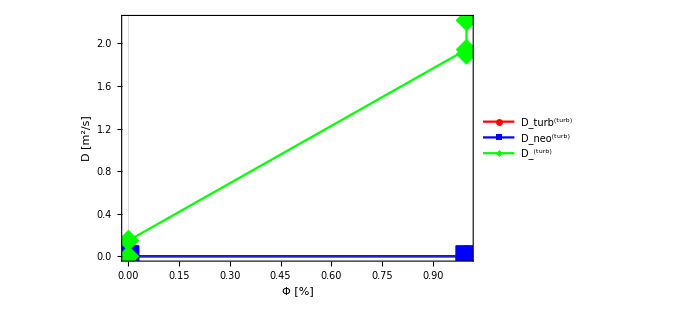

```mathematica
ListPlot[{Table[{10^2 Phi⟦i⟧,Mean[(Λ.Mean[Mean[LTT⟦i⟧]])⟦IntegerPart[(2 Nt⟦1⟧)/4];;Nt⟦1⟧⟧]},{i,nsim2}],Table[{10^2 Phi⟦i⟧,Mean[(Λ.Mean[Mean[L0T⟦i⟧]])⟦IntegerPart[(2 Nt⟦1⟧)/4];;Nt⟦1⟧⟧]},{i,nsim2}],Table[{10^2 Phi⟦i⟧,Mean[DQ1⟦i,IntegerPart[(2 Nt⟦1⟧)/3];;Nt⟦1⟧,2⟧]},{i,nsim2}]},Joined->True,PlotMarkers->{Automatic,22},PlotStyle->{Red,Blue,Green,Orange,Black},FrameLabel->{Style["Φ [%]",18,FontFamily->"Times New Roman"],Style["D [m^2/s]",18,FontFamily->"Times New Roman"]},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[{Style["D_turb^(turb)",FontFamily->"Times New Roman"],Style["D_neo^(turb)",FontFamily->"Times New Roman"],Style["D_^(turb)",FontFamily->"Times New Roman"]},{.2,.8}],PlotRange->All,PlotTheme->"Scientific"]
```

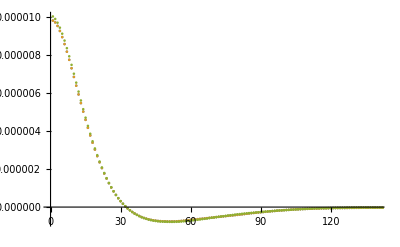

```mathematica
i=5;ListPlot[{Mean[Mean[LTT⟦i⟧]],VcorTT⟦i,1⟧,VcorTT⟦i,Nt[[1]]+1⟧//Reverse},PlotRange->{{0,140},All}]
```

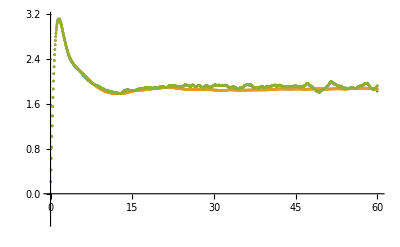

```mathematica
i=6;ListPlot[{DQ1[[i]],Transpose[{t⟦i⟧,vth⟦i⟧^2 Λ.Mean[Mean[LTT⟦i⟧+LT0⟦i⟧+L0T⟦i⟧+L00⟦i⟧]]}],Transpose[{t⟦i⟧,vth⟦i⟧^2 Total[Transpose[Λ Vcorff[[i]]]]}]},PlotRange->{All,5{-.1,.63}}]
```

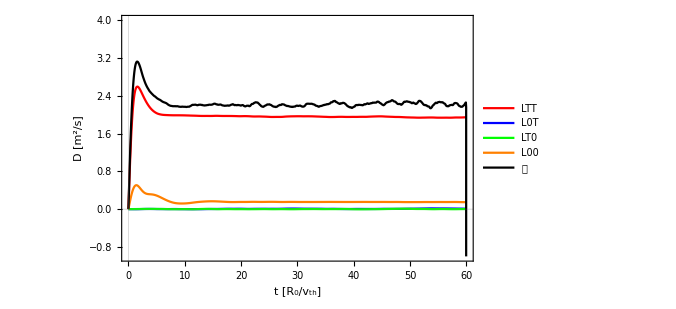

```mathematica
i=8;ListLinePlot[{{t[[i]],vth⟦i⟧^2 Λ.Mean[Mean[LTT⟦i⟧]]}//Transpose,{t[[i]],vth⟦i⟧^2 Λ.Mean[Mean[L0T⟦i⟧]]}//Transpose,{t[[i]],vth⟦i⟧^2 Λ.Mean[Mean[LT0⟦i⟧]]}//Transpose,{t[[i]],vth⟦i⟧^2 Λ.Mean[Mean[L00⟦i⟧]]}//Transpose,DQ1[[i]]},Joined->True,PlotStyle->{Red,Blue,Green,Orange,Black},PlotRange->{All,{-1,4}},FrameLabel->{Style["t [R_0/v_th]",18,FontFamily->"Times New Roman"],Style["D [m^2/s]",18,FontFamily->"Times New Roman"]},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[{Style["LTT",12,FontFamily->"Times New Roman"],Style["L0T",12,FontFamily->"Times New Roman"],Style["LT0",12,FontFamily->"Times New Roman"],Style["L00",12,FontFamily->"Times New Roman"],Style["𝒟",12,FontFamily->"Times New Roman"]},{0.9,.75}],PlotRange->All,PlotTheme->"Scientific"]
```

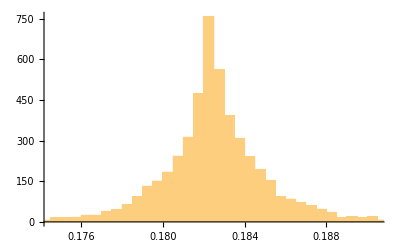

```mathematica
as=8;Sqrt[(1-kz[[as]])^2+kperp[[as]]^2]//Histogram
```

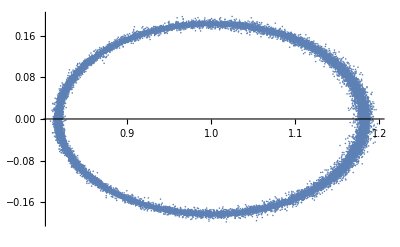

```mathematica
{kz//Flatten,kperp//Flatten}//Transpose//ListPlot
```

```mathematica
{{q1[[1,1,1,1]],q2[[1,1,1,1]]}//Transpose//ListPlot,q1[[1,1,1,1]]//ListPlot,q2[[1,1,1,1]]//ListPlot}
```

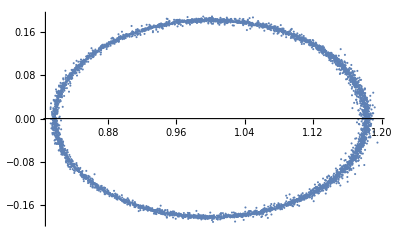

```mathematica
as=2;{kz[[as]],kperp[[as]]}//Transpose//ListPlot
```

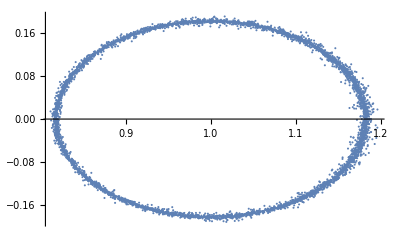

```mathematica
as=4;{kz[[as]],kperp[[as]]}//Transpose//ListPlot
```

```mathematica
𝒟full=Interpolation[Transpose[{Phi,nub,DQas}]];
𝒟turb=Interpolation[Table[{Phi⟦20i+1⟧,DQas⟦20 i+1⟧},{i,0,9}]];
𝒟coll=Interpolation[Table[{nub⟦i⟧,DQas⟦i⟧},{i,1,20}]];
```

```mathematica
full=ArrayReshape[Table[{ϕ,ν,𝒟full[ϕ,ν]},{ϕ,Min[Phi],Max[Phi],1/40 (Max[Phi]-Min[Phi])},{ν,Min[nub],Max[nub],1/40 (Max[nub]-Min[nub])}],{1600,3}];
syn=ArrayReshape[Table[{ϕ,ν,𝒟full[ϕ,ν]-𝒟turb[ϕ]-𝒟coll[ν]},{ϕ,Min[Phi],Max[Phi],1/40 (Max[Phi]-Min[Phi])},{ν,Min[nub],Max[nub],1/40 (Max[nub]-Min[nub])}],{1600,3}];grafs1={ListPlot3D[full,PlotRange->All,PlotTheme->"Scientific",LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,AxesLabel->{"Φ","ν^*","𝒟^(full)"},ColorFunction->"TemperatureMap"],ListPlot3D[syn,PlotRange->All,PlotTheme->"Scientific",LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,AxesLabel->{"Φ","ν^*","𝒟^(syn)"},ColorFunction->"TemperatureMap"],ListPlot3D[ratio,PlotRange->{{0.002,Max[Phi]},{0.02,Max[nub]},{0,1}},PlotTheme->"Scientific",LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,AxesLabel->{"Φ","ν^*","D^(syn)/D^(turb)"},ColorFunction->"TemperatureMap"]}
```

```mathematica
{,,}
```

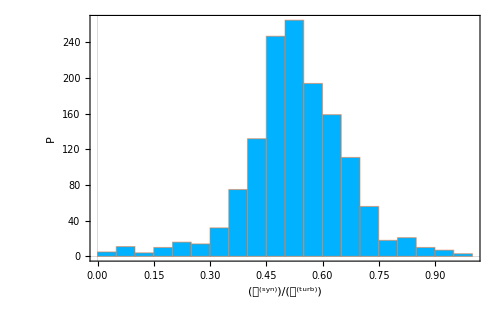

```mathematica
ratio=ArrayReshape[Table[{ϕ,ν,(𝒟full[ϕ,ν]-𝒟turb[ϕ]-𝒟coll[ν])/(Sqrt[𝒟turb[ϕ]𝒟coll[ν]]^2+0.00)},{ϕ,Min[Phi],Max[Phi],1/40 (Max[Phi]-Min[Phi])},{ν,Min[nub],Max[nub],1/40 (Max[nub]-Min[nub])}],{1600,3}];
ratio2={ratio[[All,1]],ratio[[All,2]],Mean[ratio[[All,3]]]+1.0(ratio[[All,3]]-Mean[ratio[[All,3]]])//Re}//Transpose;
hist=Histogram[ratio⟦All,3⟧,{0,1,0.05},PlotTheme->"Scientific",FrameLabel->{"𝒟^(syn)/𝒟^(turb)","P"},LabelStyle->{Black,Bold,20},ImageSize->500,ChartStyle->{Hue[.55]}]
```

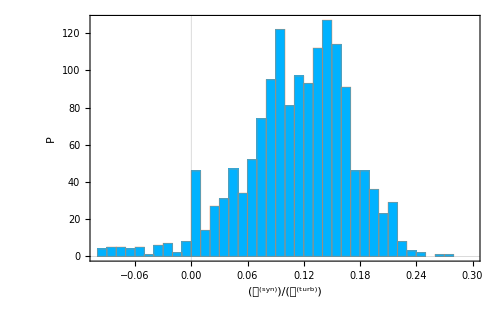

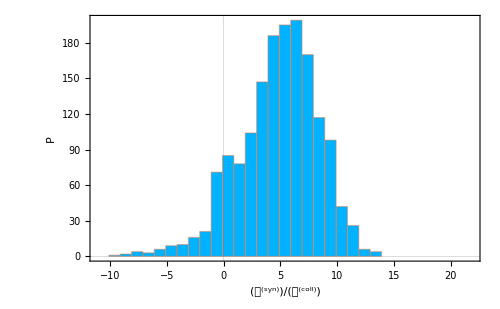

```mathematica
ratio1=ArrayReshape[Table[{ϕ,ν,(𝒟full[ϕ,ν]-𝒟turb[ϕ]-𝒟coll[ν])/(𝒟turb[ϕ])},{ϕ,Min[Phi],Max[Phi],1/40 (Max[Phi]-Min[Phi])},{ν,Min[nub],Max[nub],1/40 (Max[nub]-Min[nub])}],{1600,3}];
ratio2=ArrayReshape[Table[{ϕ,ν,(𝒟full[ϕ,ν]-𝒟turb[ϕ]-𝒟coll[ν])/(𝒟coll[ϕ])},{ϕ,Min[Phi],Max[Phi],1/40 (Max[Phi]-Min[Phi])},{ν,Min[nub],Max[nub],1/40 (Max[nub]-Min[nub])}],{1600,3}];
hist1=Histogram[ratio1⟦All,3⟧,{-.1,.3,0.01},PlotTheme->"Scientific",FrameLabel->{"𝒟^(syn)/𝒟^(turb)","P"},LabelStyle->{Black,Bold,20},ImageSize->500,ChartStyle->{Hue[.55]}]
hist2=Histogram[ratio2⟦All,3⟧,{-11.1,22.3,1},PlotTheme->"Scientific",FrameLabel->{"𝒟^(syn)/𝒟^(coll)","P"},LabelStyle->{Black,Bold,20},ImageSize->500,ChartStyle->{Hue[.55]}]
```

```mathematica
ratio[[All,3]]
```

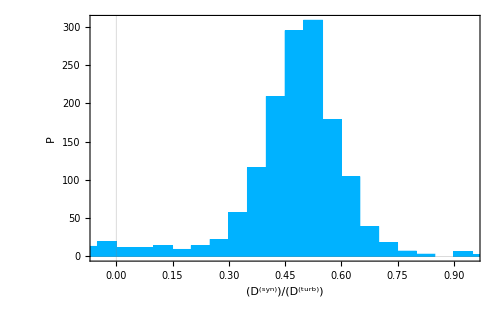

```mathematica
hist=Histogram[GaussianFilter[ratio⟦All,3⟧,1],PlotTheme->"Scientific",FrameLabel->{"D^(syn)/D^(turb)","P"},LabelStyle->{Black,Bold,20},ImageSize->500,ChartStyle->Hue[.55]]
```

```mathematica
syn//ListDensityPlot
```

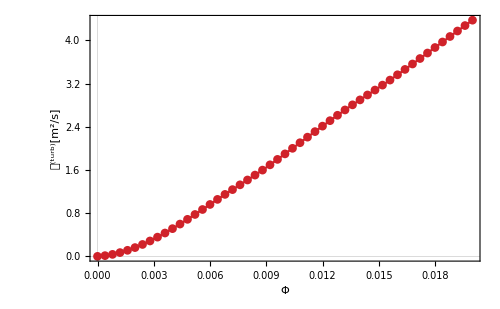
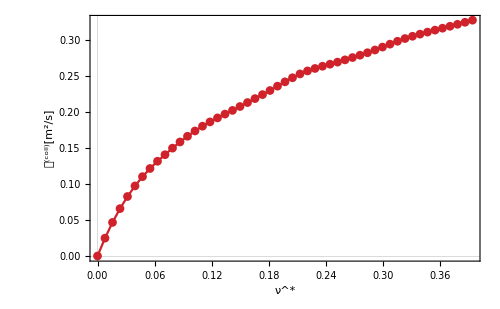

```mathematica
graf2={ListPlot[Table[{ϕ,𝒟turb[ϕ]},{ϕ,0,Max[Phi],Max[Phi]/50}],PlotTheme->"Scientific",Joined->True,PlotMarkers->Automatic,LabelStyle->{Black,Bold,20},FrameLabel->{"Φ","𝒟^(turb)[m^2/s]"},ImageSize->500,PlotStyle->"TemperatureMap"],ListPlot[Table[{ν,𝒟coll[ν]},{ν,0,Max[nub],Max[nub]/50}],Joined->True,PlotMarkers->Automatic,PlotTheme->"Scientific",LabelStyle->{Black,Bold,20},FrameLabel->{"ν^*","𝒟^(coll)[m^2/s]"},ImageSize->500,PlotStyle->"TemperatureMap"]}
```

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_1_a.eps

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_1_b.eps

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_2_a.eps

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_2_b.eps

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_2_c.eps

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_3.eps

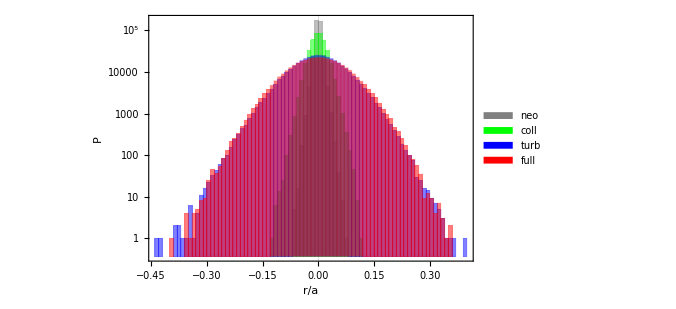

```mathematica
Export[expfoto<>"fig_1_a.eps",graf2[[1]]]
Export[expfoto<>"fig_1_b.eps",graf2[[2]]]
Export[expfoto<>"fig_2_a.eps",grafs1[[1]]]
Export[expfoto<>"fig_2_b.eps",grafs1[[2]]]
Export[expfoto<>"fig_2_c.eps",grafs1[[3]]]
Export[expfoto<>"fig_3.eps",hist]
```

```mathematica
Export[expfoto<>"fig_4.eps",histo]
```

F:\5_Plasma\2_Present\1_Neo_Turb_Synergies\Arxiv\fig_4.eps

```mathematica
{size1,size2}={17,17};legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->size1],Style["t = t_0",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->size1],Style["t = t_max",size2,FontFamily->"Times New Roman"]}}];fig1a=ListPlot[{Transpose[{kz[[1]]//Flatten,kperp[[1]]//Flatten}],Transpose[{kx[[1]]//Flatten,ky[[1]]//Flatten}]},PlotTheme->"Scientific",FrameLabel->{"R/R_0","Z/R_0"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotStyle->{Blue,Red},AspectRatio->Full,PlotLegends->Placed[legend,{0.85,0.08}]]
fig1b=ListPlot[{Transpose[{kz[[2]]//Flatten,kperp[[2]]//Flatten}],Transpose[{kx[[2]]//Flatten,ky[[2]]//Flatten}]},PlotTheme->"Scientific",FrameLabel->{"R/R_0","Z/R_0"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotStyle->{Blue,Red},AspectRatio->Full,PlotLegends->Placed[legend,{0.85,0.08}]]
```

```mathematica
Export[expfoto<>"fig_1_a.eps",fig1a,"AllowRasterization"->True]
Export[expfoto<>"fig_1_b.eps",fig1b,"AllowRasterization"->True]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_1_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_1_b.eps

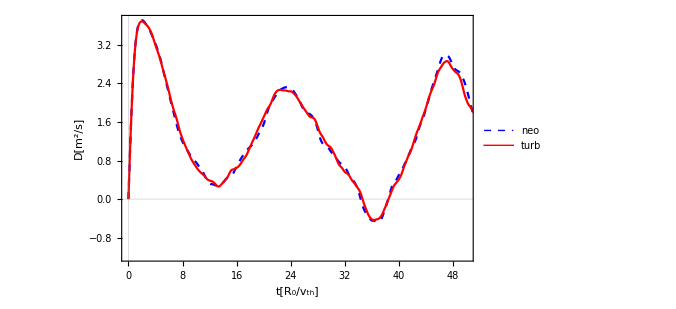

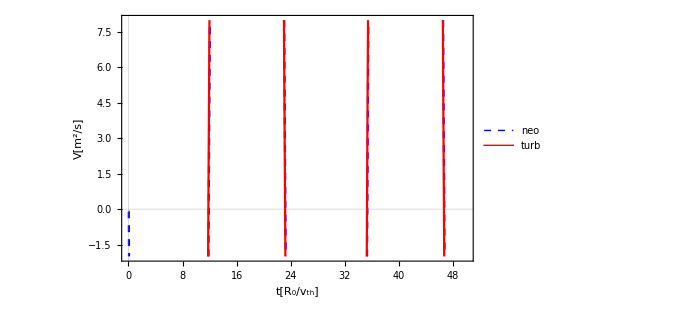

```mathematica
legend=Grid[{{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->15],Style["neo",FontFamily->"Times New Roman",18]},{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->15],Style["turb",FontFamily->"Times New Roman",18]}}];
fig2a=ListLinePlot[DQ1,PlotRange->{{0,50},All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},PlotStyle->{{Blue,Dashed},Red,Green,Brown,Black},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[legend,{0.75,0.75}]]
fig2b=ListLinePlot[VQ1,PlotRange->{{0,50},{-2,8}},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","V[m^2/s]"},PlotStyle->{{Blue,Dashed},Red,Green,Brown,Black},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[legend,{0.75,0.75}]]
```

```mathematica
Export[expfoto<>"fig_2_a.eps",fig2a]
Export[expfoto<>"fig_2_b.eps",fig2b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_2_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_2_b.eps

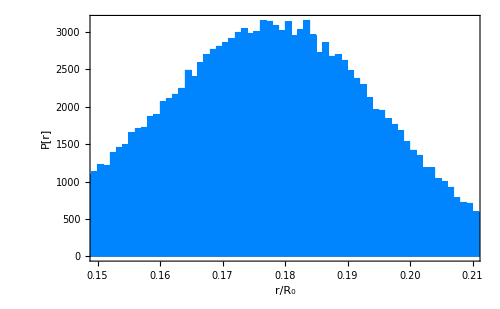

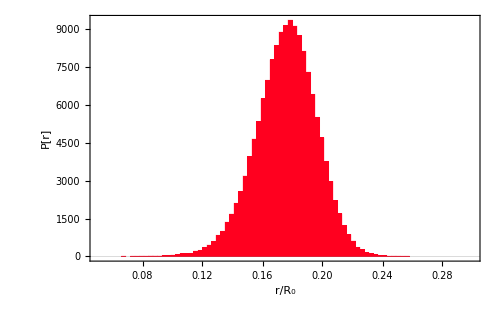

```mathematica
i=1;fig3a=Histogram[√((kz[[i]]-1)^2+kperp[[i]]^2)//Flatten,{0.001},PlotRange->{{0.15,0.21},All},PlotTheme->"Scientific",FrameLabel->{"r/R_0","P[r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->Hue[.58]]
i=2;fig3b=Histogram[√((kz[[i]]-1)^2+kperp[[i]]^2)//Flatten,{0.003},PlotRange->{{0.05,0.3},All},PlotTheme->"Scientific",FrameLabel->{"r/R_0","P[r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->Hue[.98]]
```

```mathematica
Export[expfoto<>"fig_3_a.eps",fig3a]
Export[expfoto<>"fig_3_b.eps",fig3b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_3_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_3_b.eps

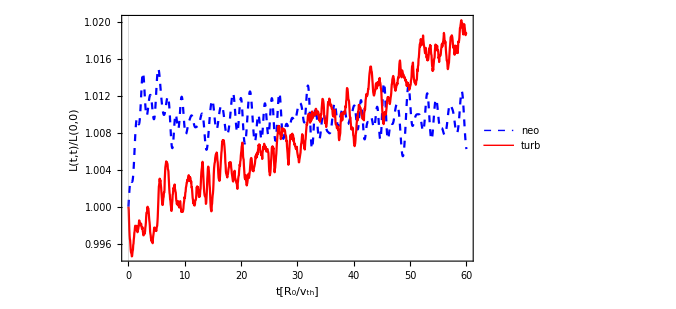

```mathematica
legend=Grid[{{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->15],Style["neo",FontFamily->"Times New Roman",18]},{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->15],Style["turb",FontFamily->"Times New Roman",18]}}];
fig4=ListLinePlot[Table[{t[[i]],Diagonal[Vcorff⟦i⟧]/(Diagonal[Vcorff⟦i⟧][[1]])}//Transpose,{i,2}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L(t,t)/L(0,0)"},PlotStyle->{{Blue,Dashed},Red,Green,Brown,Black},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[legend,{0.75,0.25}]]
```

```mathematica
Export[expfoto<>"fig_4.eps",fig4]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_4.eps

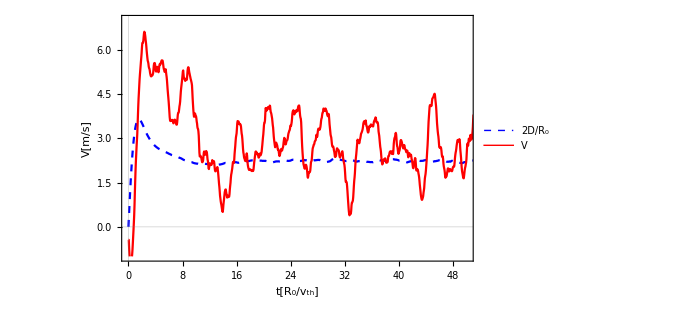

```mathematica
i=2;legend=Grid[{{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->15],Style["2D/R_0",FontFamily->"Times New Roman",18]},{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->15],Style["V",FontFamily->"Times New Roman",18]}}];fig5=ListLinePlot[{{t[[i]],(2 DQ1⟦i,All,2⟧)/R0⟦i⟧}//Transpose,VQ1[[i]]},PlotRange->{{0,50},{-1,7}},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","V[m/s]"},PlotStyle->{{Blue,Dashed},Red,Green,Brown,Black},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[legend,{0.75,0.85}]]
```

```mathematica
Export[expfoto<>"fig_5.eps",fig5]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_5.eps

```mathematica
jj=1;pas=5;fig6a=ListDensityPlot[ArrayReshape[Table[{tmax[[jj]] pas i/Nt[[jj]],tmax[[jj]] pas j/Nt[[jj]],10^6 Vcorff⟦jj,pas i,pas j⟧},{i,Nt[[jj]]/pas },{j,Nt[[jj]]/pas }],{(Nt[[jj]]/pas)^2//IntegerPart,3}],PlotRange->All,PlotTheme->"Scientific",PlotRange->All,FrameLabel->{"t[R_0/v_th]","t'[R_0/v_th]","L(t,t')[10^-6v_th^2]"},ColorFunction->"TemperatureMap",PlotLegends->Automatic,LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
jj=2;pas=5;fig6b=ListDensityPlot[ArrayReshape[Table[{tmax[[jj]] pas i/Nt[[jj]],tmax[[jj]] pas j/Nt[[jj]],10^6 Vcorff⟦jj,pas i,pas j⟧},{i,Nt[[jj]]/pas },{j,Nt[[jj]]/pas }],{(Nt[[jj]]/pas)^2//IntegerPart,3}],PlotRange->All,PlotTheme->"Scientific",PlotRange->All,FrameLabel->{"t[R_0/v_th]","t'[R_0/v_th]","L(t,t')[10^-6v_th^2]"},ColorFunction->"TemperatureMap",PlotLegends->Automatic,LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Export[expfoto<>"fig_6_a.eps",fig6a,"AllowRasterization"->True]
Export[expfoto<>"fig_6_b.eps",fig6b,"AllowRasterization"->True]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_6_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_6_b.eps

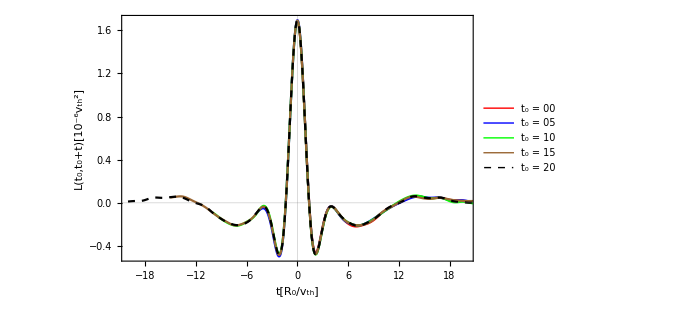

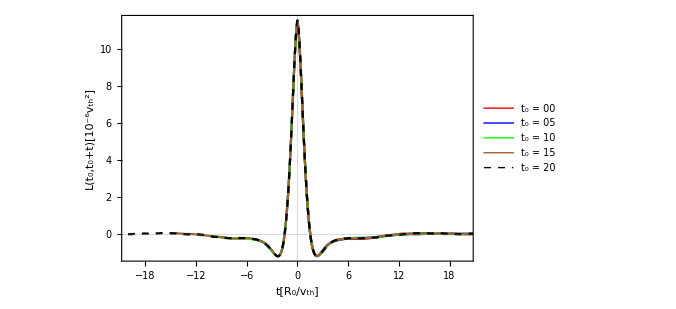

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["t_0 = 00",size2,FontFamily->"Times New Roman",Bold]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["t_0 = 05",size2,FontFamily->"Times New Roman",Bold]},{Graphics[{Green,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["t_0 = 10",size2,FontFamily->"Times New Roman",Bold]},{Graphics[{Brown,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["t_0 = 15",size2,FontFamily->"Times New Roman",Bold]},{Graphics[{Black,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["t_0 = 20",size2,FontFamily->"Times New Roman",Bold]}}];ja=1;Luri=Table[{δt*dt[[1]],10^6 Vcorff⟦ja,tbase1,tbase1+δt⟧},{ja,2},{tbase1,2,402,100},{δt,-tbase1+1,Nt⟦1⟧+1-tbase1}];
fig7a=ListLinePlot[Luri[[1]],PlotRange->{{-20,20},All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L(t_0,t_0+t)[10^-6v_th^2]"},PlotStyle->{Red,Blue,Green,Brown,{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
fig7b=ListLinePlot[Luri[[2]],PlotRange->{{-20,20},All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L(t_0,t_0+t)[10^-6v_th^2]"},PlotStyle->{Red,Blue,Green,Brown,{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Export[expfoto<>"fig_7_a.eps",fig7a]
Export[expfoto<>"fig_7_b.eps",fig7b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_7_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_7_b.eps

```mathematica
vth*3.2*10^-4
```

{70.031,70.031}

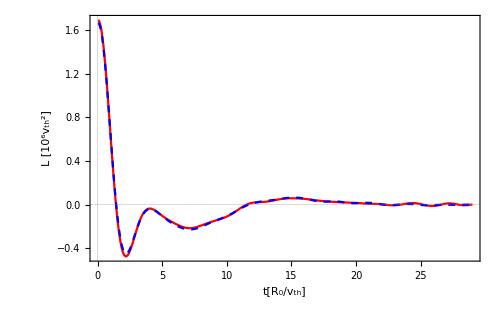

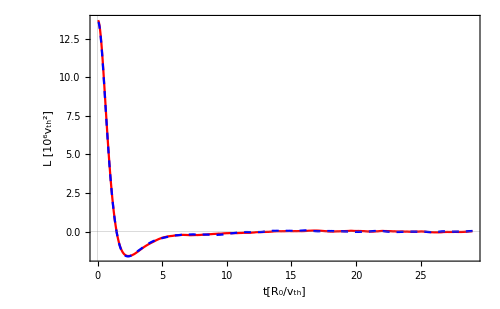

```mathematica
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(t_0,t_0+t)",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(0,t)    ",size2,FontFamily->"Times New Roman"]},{Graphics[{},ImageSize->size1],Style["t_0 = 30",size2,FontFamily->"Times New Roman"]}}];
i=1;tbase=620;fig8a=ListLinePlot[{Table[{τ dt[[i]],10^6 Vcorff⟦i,tbase+1,tbase+τ⟧},{τ,1,Nt[[i]]-tbase,1}],Table[{τ dt[[i]],10^6 Vcorff⟦i,1,τ⟧},{τ,1,Nt[[i]]-tbase,1}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L [10^-6v_th^2]"},PlotStyle->{Red,{Blue,Dashed},Green,Brown,Black},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
i=2;fig8b=ListLinePlot[{Table[{τ dt[[i]],10^6 Vcorff⟦i,tbase+1,tbase+τ⟧},{τ,1,Nt[[i]]-tbase,1}],Table[{τ dt[[i]],10^6 Vcorff⟦i,1,τ⟧},{τ,1,Nt[[i]]-tbase,1}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L [10^-6v_th^2]"},PlotStyle->{Red,{Blue,Dashed},Green,Brown,Black},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

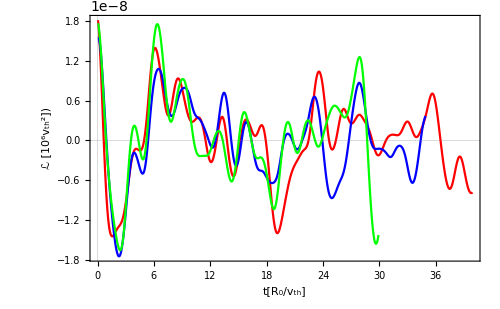

```mathematica
i=1;tbase=800;fig11a=ListLinePlot[Table[{τ dt[[i]],Vcorff⟦i,tbase+2,tbase+τ⟧-Vcorff⟦i,2,τ⟧},{tbase,402,602,100},{τ,1,Nt[[i]]-tbase,1}],PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","ℒ [10^6v_th^2])"},PlotStyle->{Red,Blue,Green,Brown,Black},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
i=2;fig9b=ListLinePlot[Table[{τ dt[[i]],Vcorff⟦i,tbase+2,tbase+τ⟧-Vcorff⟦i,2,τ⟧},{tbase,102,502,100},{τ,1,Nt[[i]]-tbase,1}],PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","ℒ [10^6v_th^2])"},PlotStyle->{Red,Blue,Green,Brown,Black},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Export[expfoto<>"fig_8_a.eps",fig8a]
Export[expfoto<>"fig_8_b.eps",fig8b]
```

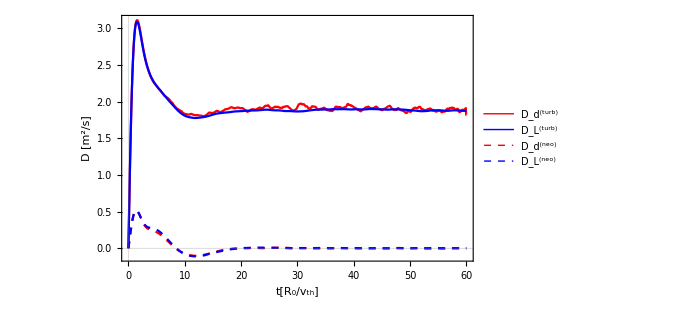

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_d^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Red,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_d^(neo)",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_L^(neo)",size2,FontFamily->"Times New Roman"]}}];fig9=ListLinePlot[{DQ1[[2]],Transpose[{t⟦1⟧,vth⟦1⟧^2 Λ.Vcorff⟦2,1⟧}],DQ1[[1]],Transpose[{t⟦1⟧,vth⟦1⟧^2 Λ.Vcorff⟦1,1⟧}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D [m^2/s]"},PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},PlotLegends->Placed[legend,{0.8,0.3}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Export[expfoto<>"fig_9.eps",fig9]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_9.eps

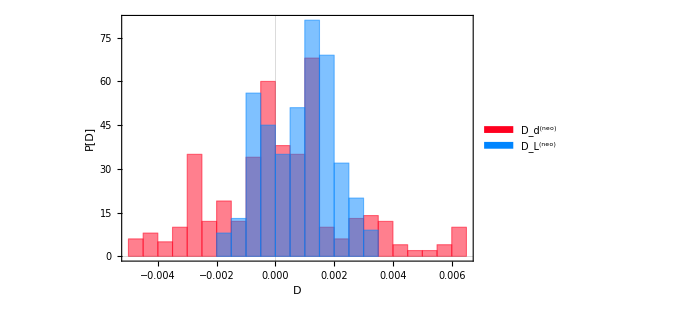

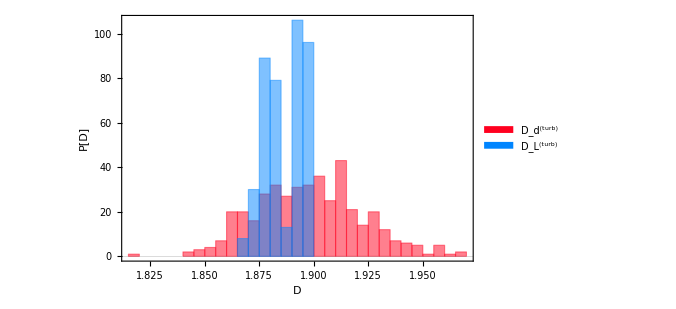

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["D_d^(neo)",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["D_L^(neo)",size2,FontFamily->"Times New Roman"]}}];i=1;frac=0.65;
kek1=DQ1⟦i,IntegerPart[frac Nt⟦i⟧];;Nt⟦i⟧-2,2⟧;
kek2=vth⟦i⟧^2 (Λ.Vcorff⟦i,1⟧)⟦IntegerPart[frac Nt⟦i⟧];;Nt⟦i⟧-2⟧;
fig10a=Histogram[{kek1-0Mean[kek1],kek2-0Mean[kek2]},{0.0005},PlotTheme->"Scientific",FrameLabel->{"D","P[D]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.98],Hue[.58]},ChartLegends->Placed[legend,{0.9,0.55}]]
i=2;
legend=Grid[{{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["D_d^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]}}];kek1=DQ1⟦i,IntegerPart[frac Nt⟦i⟧];;Nt⟦i⟧,2⟧;
kek2=vth⟦i⟧^2 (Λ.Vcorff⟦i,1⟧)⟦IntegerPart[frac Nt⟦i⟧];;Nt⟦i⟧⟧;
fig10b=Histogram[{kek1-0Mean[kek1],kek2-0Mean[kek2]},{0.005},PlotTheme->"Scientific",FrameLabel->{"D","P[D]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.98],Hue[.58]},ChartLegends->Placed[legend,{0.9,0.55}]]
```

```mathematica
Export[expfoto<>"fig_10_a.eps",fig10a]
Export[expfoto<>"fig_10_b.eps",fig10b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_10_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_10_b.eps

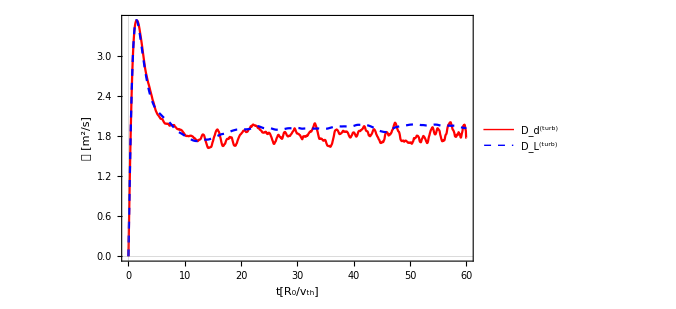

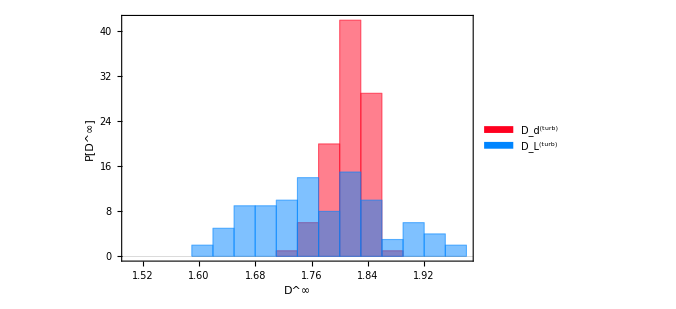

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_d^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]}}];frac=0.7;DQasyD=Table[DQ1[[i,frac Nt[[1]];;Nt[[1]]-13,2]]//Mean,{i,nsim2}];DQasyL=Table[vth⟦i⟧^2 (Λ.Vcorff⟦i,1⟧)[[frac Nt[[1]];;Nt[[1]]-13]]//Mean,{i,nsim2}];i=11;
fig11a=ListLinePlot[{DQ1⟦i⟧,Transpose[{t⟦i⟧,vth⟦i⟧^2 Λ.Vcorff⟦i,1⟧}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D [m^2/s]"},PlotStyle->{Red,{Blue,Dashed}},PlotLegends->Placed[legend,{0.8,0.75}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
legend=Grid[{{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["D_d^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]}}];
fig11b=Histogram[{DQasyD,DQasyL},{1.5,2.,0.03},PlotTheme->"Scientific",FrameLabel->{"D^∞","P[D^∞]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.98],Hue[.58]},ChartLegends->Placed[legend,{0.9,0.55}]]
```

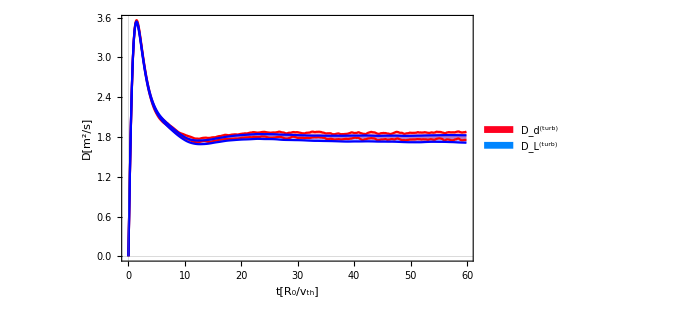

```mathematica
Needs["ErrorBarPlots`"];statistiD=Table[{t⟦1,j⟧,Mean[DQ1⟦All,j,2⟧],Sqrt[Mean[DQ1⟦All,j,2⟧^2]-Mean[DQ1⟦All,j,2⟧]^2]},{j,1,Nt⟦1⟧-1}];
DL=Table[Λ.Vcorff⟦i,1⟧,{i,nsim2}];
statistiL=Table[{t⟦1,j⟧,vth⟦1⟧^2 Mean[DL⟦All,j⟧],vth⟦1⟧^2(Sqrt[Mean[DL⟦All,j⟧^2]-Mean[DL⟦All,j⟧]^2])},{j,1,Nt⟦1⟧-1}];legend=Grid[{{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["D_d^(turb)",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["D_L^(turb)",size2,FontFamily->"Times New Roman"]}}];
fig11c=ListLinePlot[{Transpose[{statistiD⟦All,1⟧,statistiD⟦All,2⟧+1/2 statistiD⟦All,3⟧}],Transpose[{statistiD⟦All,1⟧,statistiD⟦All,2⟧-1/2 statistiD⟦All,3⟧}],Transpose[{statistiL⟦All,1⟧,statistiL⟦All,2⟧+1/2 statistiL⟦All,3⟧}],Transpose[{statistiL⟦All,1⟧,statistiL⟦All,2⟧-1/2 statistiL⟦All,3⟧}]},Filling->{1->{2},3->{4}},PlotStyle->{Red,Red,Blue,Blue},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotLegends->Placed[legend,{0.9,0.25}]]
```

```mathematica
Export[expfoto<>"fig_11_a.eps",fig11a]
Export[expfoto<>"fig_11_b.eps",fig11b]
Export[expfoto<>"fig_11_c.eps",fig11c]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_11_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_11_b.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_11_c.eps

```mathematica
(*Np behaviour of Dd & DL errors*)
```

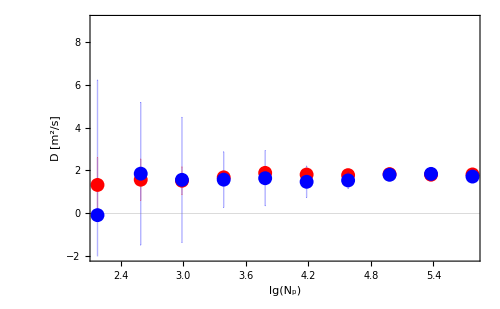

```mathematica
frac=0.6;difD=Table[Mean[((rhoi⟦i⟧^2 (RotateLeft[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]-RotateRight[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]))/((R0⟦i⟧ (4 dt⟦i⟧))/vth⟦i⟧))⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];
difD=Transpose[Table[{Mean[difD⟦i⟧],√Mean[(difD⟦i⟧-Mean[difD⟦i⟧])^2]},{i,nsim2}]];frac=0.6;difL=Table[vth⟦i⟧^2 Mean[(Λ.Vcorff⟦i,1,j,1⟧)⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];difL=Transpose[Table[{Mean[difL⟦i⟧],√Mean[(difL⟦i⟧-Mean[difL⟦i⟧])^2]},{i,nsim2}]];Needs["ErrorBarPlots`"]
legend=Grid[{{Graphics[{Red,Disk[]},ImageSize->8],Style["D_d",12,Bold,FontFamily->"Times New Roman"]},{Graphics[{Blue,Disk[]},ImageSize->8],Style["D_L",12,Bold,FontFamily->"Times New Roman"]},{Graphics[{Black,Thick,Line[{{0,0},{2,0}}]},ImageSize->8],Style["~ N_p^(-1/2)",12,Bold,FontFamily->"Times New Roman"]}}];g1=ListPlot[{Transpose[{Np*Nloop, difD⟦2⟧}]//Log,Transpose[{Np*Nloop, difL⟦2⟧}]//Log,Table[{aa,15 aa^(-1/2)},{aa,Min[Np Nloop],Max[Np  Nloop],200}]//Log},PlotTheme->"Scientific",PlotRange->{All,All},FrameLabel->{"lg(N_p)","lg(σ)"},LabelStyle->{Black,Bold,12,FontFamily->"Times New Roman"},ImageSize->250,PlotStyle->{{Red,PointSize[0.03]},{Blue,PointSize[0.03]},Black},Joined->{False,False,True},PlotLegends->Placed[legend,{.86,.75}]];fig18a=ListPlot[{Transpose[{Log[10,Np Nloop],difD⟦1⟧-difD⟦2⟧}],Transpose[{Log[10,Np Nloop],difD⟦1⟧+0difD⟦2⟧}],Transpose[{Log[10,Np Nloop],difD⟦1⟧+difD⟦2⟧}],Transpose[{Log[10,Np Nloop],difL⟦1⟧-difL⟦2⟧}],Transpose[{Log[10,Np Nloop],difL⟦1⟧+0difL⟦2⟧}],Transpose[{Log[10,Np Nloop],difL⟦1⟧+difL⟦2⟧}]},Joined->False,PlotTheme->"Scientific",PlotRange->{All,{-2,9}},FrameLabel->{"lg(N_p)","D [m^2/s]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotStyle->{{Red,PointSize[0.001]},{Red,PointSize[0.02]},{Red,PointSize[0.001]},{Blue,PointSize[0.001]},{Blue,PointSize[0.02]},{Blue,PointSize[0.001]}},Epilog->Inset[g1,{4.8,5.7}],Filling->{1->{3},4->{6}},FillingStyle->{Thick,Thick}]
```

```mathematica
frac=0.9;difD=Table[Mean[((rhoi⟦i⟧^2 (RotateLeft[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]-RotateRight[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]))/((R0⟦i⟧ (4 dt⟦i⟧))/vth⟦i⟧))⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];
difL=Table[vth⟦i⟧^2 Mean[(Λ.Vcorff⟦i,1,j,1⟧)⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];
```

```mathematica
difD=Table[Mean[((rhoi⟦i⟧^2 (RotateLeft[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]-RotateRight[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]))/((R0⟦i⟧ (4 dt⟦i⟧))/vth⟦i⟧))⟦(1-frc*0.05) Nt⟦i⟧;;Nt⟦i⟧-2⟧],{frc,1,10},{i,nsim2},{j,Nloop⟦1⟧}];difL=Table[vth⟦i⟧^2 Mean[(Λ.Vcorff⟦i,1,j,1⟧)⟦(1-frc*0.05) Nt⟦i⟧;;Nt⟦i⟧-2⟧],{frc,1,10},{i,nsim2},{j,Nloop⟦1⟧}];
```

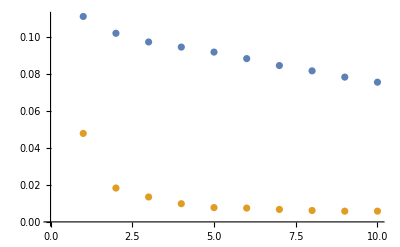

```mathematica
ListPlot[{Table[Mean[Flatten[difL⟦o⟧^2]]-Mean[Flatten[difL⟦o⟧]]^2,{o,10}],Table[Mean[Flatten[difD⟦o⟧^2]]-Mean[Flatten[difD⟦o⟧]]^2,{o,10}]}]
```

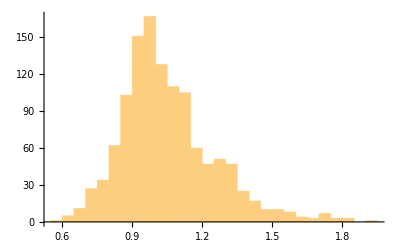

```mathematica
Histogram[Flatten[difD]/Flatten[difL]]
```

```mathematica
difD//Flatten//Mean
```

1.8345

```mathematica
difL//Flatten//Mean
```

1.79714

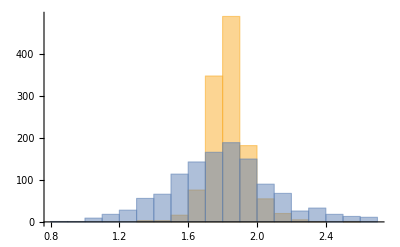

```mathematica
{difD//Flatten,difL//Flatten}//Histogram
```

```mathematica
frac=0.6;difD=Table[Mean[((rhoi⟦i⟧^2 (RotateLeft[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]-RotateRight[Q2⟦i,1,j⟧-Q1⟦i,1,j⟧^2]))/((R0⟦i⟧ (4 dt⟦i⟧))/vth⟦i⟧))⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];
difD=Transpose[Table[{Mean[difD⟦i⟧],√Mean[(difD⟦i⟧-Mean[difD⟦i⟧])^2]},{i,nsim2}]];frac=0.6;difL=Table[vth⟦i⟧^2 Mean[(Λ.Vcorff⟦i,1,j,1⟧)⟦frac Nt⟦i⟧;;Nt⟦i⟧-2⟧],{i,nsim2},{j,Nloop⟦1⟧}];difL=Transpose[Table[{Mean[difL⟦i⟧],√Mean[(difL⟦i⟧-Mean[difL⟦i⟧])^2]},{i,nsim2}]];Needs["ErrorBarPlots`"]
legend=Grid[{{Graphics[{Red,Disk[]},ImageSize->8],Style["D_d",12,Bold,FontFamily->"Times New Roman"]},{Graphics[{Blue,Disk[]},ImageSize->8],Style["D_L",12,Bold,FontFamily->"Times New Roman"]},{Graphics[{Black,Thick,Line[{{0,0},{2,0}}]},ImageSize->8],Style["~ N_p^(-1/2)",12,Bold,FontFamily->"Times New Roman"]}}];g1=ListPlot[{Transpose[{Nc, difD⟦2⟧}],Transpose[{Nc, difL⟦2⟧}],Table[{aa,15 aa^(-1/2)},{aa,Min[Nc ],Max[Nc ],200}]},PlotTheme->"Scientific",PlotRange->{All,{0,1}},FrameLabel->{"lg(N_p)","lg(σ)"},LabelStyle->{Black,Bold,12,FontFamily->"Times New Roman"},ImageSize->250,PlotStyle->{{Red,PointSize[0.03]},{Blue,PointSize[0.03]},Black},Joined->{False,False,True},PlotLegends->Placed[legend,{.86,.75}]];fig18b=ListPlot[{Transpose[{Nc,difD⟦1⟧-difD⟦2⟧}],Transpose[{Nc,difD⟦1⟧+0difD⟦2⟧}],Transpose[{Nc,difD⟦1⟧+difD⟦2⟧}],Transpose[{Nc,difL⟦1⟧-difL⟦2⟧}],Transpose[{Nc,difL⟦1⟧+0difL⟦2⟧}],Transpose[{Nc,difL⟦1⟧+difL⟦2⟧}]},Joined->False,PlotTheme->"Scientific",PlotRange->{All,{1.,4}},FrameLabel->{"lg(N_p)","D [m^2/s]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotStyle->{{Red,PointSize[0.001]},{Red,PointSize[0.02]},{Red,PointSize[0.001]},{Blue,PointSize[0.001]},{Blue,PointSize[0.02]},{Blue,PointSize[0.001]}},Epilog->Inset[g1,{68,3.}],Filling->{1->{3},4->{6}},FillingStyle->{Thick,Thick}]
```

```mathematica
Export[expfoto<>"fig_18_b.eps",fig18b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_18_b.eps

```mathematica
Export[expfoto<>"fig_18.eps",fig18a]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_18.eps

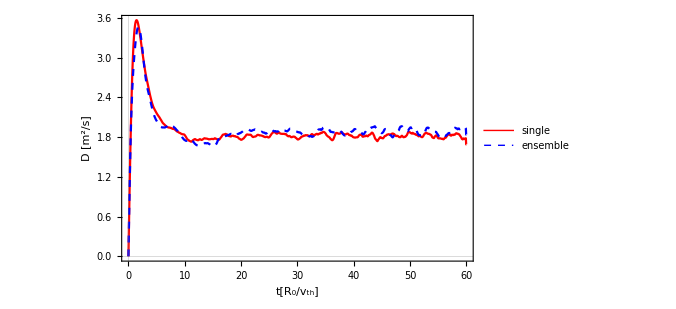

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["single",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["ensemble",size2,FontFamily->"Times New Roman"]}}];fig12=ListLinePlot[DQ1,PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D [m^2/s]"},PlotStyle->{Red,{Blue,Dashed}},PlotLegends->Placed[legend,{0.8,0.25}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Export[expfoto<>"fig_12.eps",fig12]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_12.eps

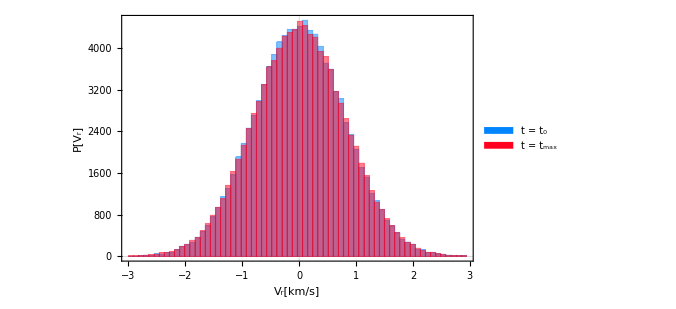

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["t = t_0   ",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["t = t_max",size2,FontFamily->"Times New Roman"]}}];i=1;fig13a=Histogram[{10^-3 vth[[i]]w[[i]]//Flatten,10^-3 vth[[i]]ph[[i]]//Flatten},{-1,1,.03},PlotTheme->"Scientific",FrameLabel->{"V_r[km/s]","P[V_r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.58],Hue[.98]},ChartLegends->Placed[legend,{0.9,0.55}]]
i=2;fig13b=Histogram[{10^-3 vth[[i]]w[[i]]//Flatten,10^-3 vth[[i]]ph[[i]]//Flatten},{-3,3,0.09},PlotTheme->"Scientific",FrameLabel->{"V_r[km/s]","P[V_r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.58],Hue[.98]},ChartLegends->Placed[legend,{0.9,0.55}]]
```

```mathematica
Export[expfoto<>"fig_13_a.eps",fig13a]
Export[expfoto<>"fig_13_b.eps",fig13b]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_13_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_13_b.eps

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["⟨∂_y ϕ(t)^2⟩/⟨∂_y ϕ(0)^2⟩",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["⟨∂_x ϕ(t)^2⟩/⟨∂_x ϕ(0)^2⟩",size2,FontFamily->"Times New Roman"]},{Graphics[{Black,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["⟨J_0(k_⊥ρ)⟩",size2,FontFamily->"Times New Roman"]}}];
fig14a=ListLinePlot[{{t[[1]],Diagonal[VcorTT//Mean](3/lambday[[1]]^2+k0i[[1]]^2)^-1}//Transpose,{t[[1]],lambdax[[1]]^2Diagonal[Vcorff//Mean]}//Transpose,{t[[1]],0.833+0t[[1]]}//Transpose},PlotRange->{All,{0.825,0.849}},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","⟨∂_i ϕ(t)^2⟩/⟨∂_i ϕ(0)^2⟩"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]

legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["⟨∂_x ϕ⟩",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["⟨∂_y ϕ⟩",size2,FontFamily->"Times New Roman"]}}];
fig14b=ListLinePlot[{{t[[1]],Mean[Mean[Mean[V0+VT]]]/Sqrt[Diagonal[Vcorff//Mean]]}//Transpose,{t[[1]],Mean[Mean[Mean[VT]]]/Sqrt[Diagonal[VcorTT//Mean]]}//Transpose},PlotRange->{All,{-0.015,0.008}},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","⟨∂_i ϕ(t)⟩/√⟨SubscriptBox[∂, i]ϕ SuperscriptBox[(t), 2]⟩"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
{size1,size2}={15,18};legend=Grid[{{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["t = t_0",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["t = t_max",size2,FontFamily->"Times New Roman"]}}];fig14c=Histogram[{(3/lambday[[1]]^2+k0i[[1]]^2)^(-1/2) w//Flatten,(3/lambday[[1]]^2+k0i[[1]]^2)^(-1/2)ph//Flatten},{-4,4,.05},PlotTheme->"Scientific",FrameLabel->{"∂_y ϕ","P[∂_y ϕ]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.58],Hue[.98]},ChartLegends->Placed[legend,{0.9,0.55}]]
```

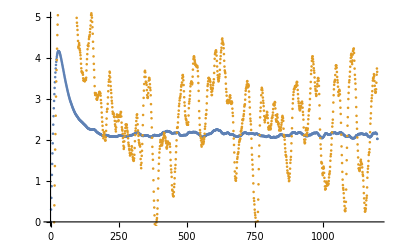

```mathematica
ListPlot[{2/R0[[1]]Mean[DQ1[[All,All,2]]],Mean[VQ1[[All,All,2]]]}]
```

```mathematica
Export[expfoto<>"fig_14_a.eps",fig14a]
Export[expfoto<>"fig_14_b.eps",fig14b]
Export[expfoto<>"fig_14_c.eps",fig14c]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_14_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_14_b.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_14_c.eps

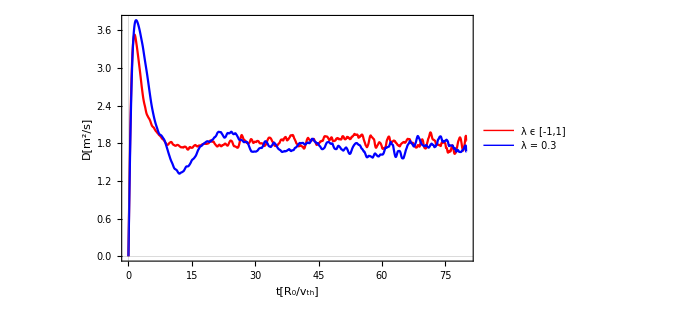

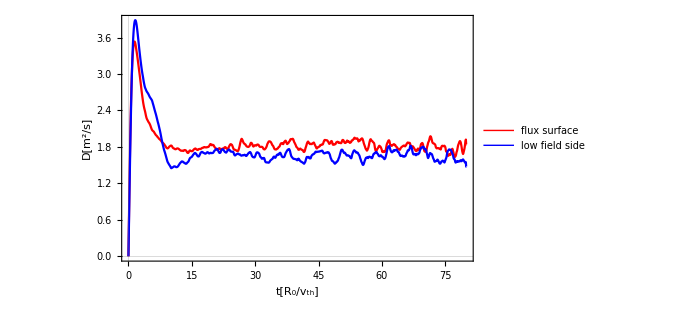

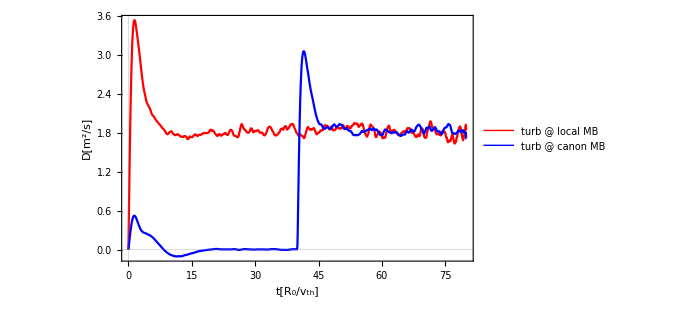

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["λ ϵ [-1,1]",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["λ = 0.3   ",size2,FontFamily->"Times New Roman"]}}];
fig15a=ListLinePlot[{DQ1[[1;;2]]//Mean,DQ1[[3;;4]]//Mean},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["E ϵ MB",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style[" E = T_i   ",size2,FontFamily->"Times New Roman"]}}];
fig15b=ListLinePlot[{DQ1[[1;;2]]//Mean,DQ1[[5;;6]]//Mean},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["flux surface",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style[" low field side",size2,FontFamily->"Times New Roman"]}}];
fig15c=ListLinePlot[{DQ1[[1;;2]]//Mean,DQ1[[7;;8]]//Mean},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["turb @ local MB",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["turb @ canon MB",size2,FontFamily->"Times New Roman"]}}];
fig15d=ListLinePlot[{DQ1[[1;;2]]//Mean,DQ1[[9;;10]]//Mean},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D[m^2/s]"},PlotStyle->{Red,{Blue},{Black,Dashed}},PlotLegends->Placed[legend,{0.8,0.85}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Export[expfoto<>"fig_15_a.eps",fig15a]
Export[expfoto<>"fig_15_b.eps",fig15b]
Export[expfoto<>"fig_15_c.eps",fig15c]
Export[expfoto<>"fig_15_d.eps",fig15d]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_15_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_15_b.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_15_c.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_15_d.eps

```mathematica
nf;tf;nb;tb;
tb;tf;nb;nf;
deci 4-1;2->2;1->4;
```

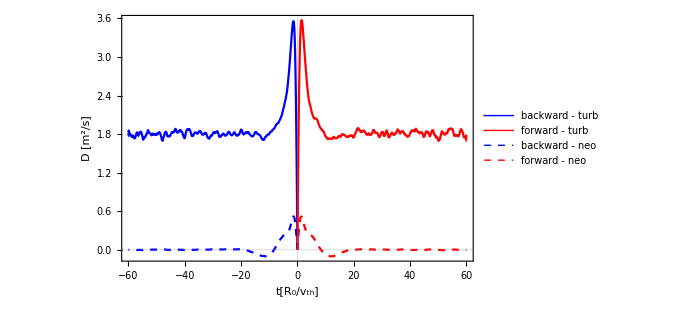

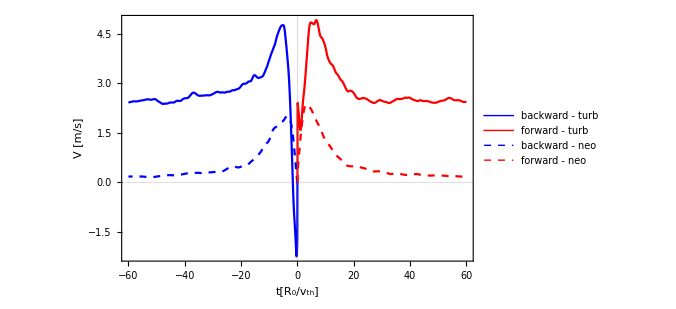

```mathematica
mask=Table[{1,-1},{i,Length[DQ1[[1]]]}];{size1,size2}={15,18};legend=Grid[{{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["backward - turb",size2,FontFamily->"Times New Roman"]},{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["forward - turb",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["backward - neo",size2,FontFamily->"Times New Roman"]},{Graphics[{Red,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["forward - neo",size2,FontFamily->"Times New Roman"]}}];
fig16a=ListLinePlot[{mask DQ1[[1]],DQ1[[2]],mask DQ1[[3]],DQ1[[4]]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D [m^2/s]"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[legend,{0.8,0.8}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
fig16b=ListLinePlot[{mask VQ2[[1]],VQ2[[2]],mask VQ2[[3]],VQ2[[4]]},PlotRange->{All,Automatic},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","V [m/s]"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[legend,{0.8,0.8}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

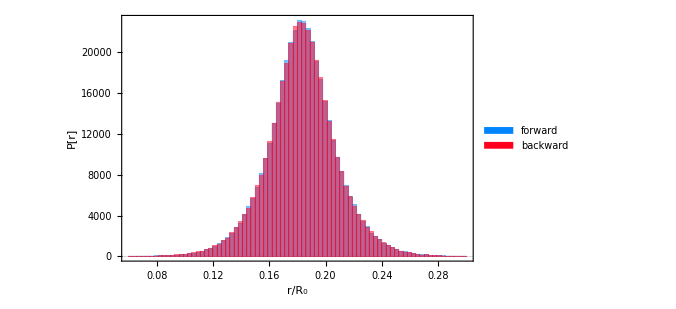

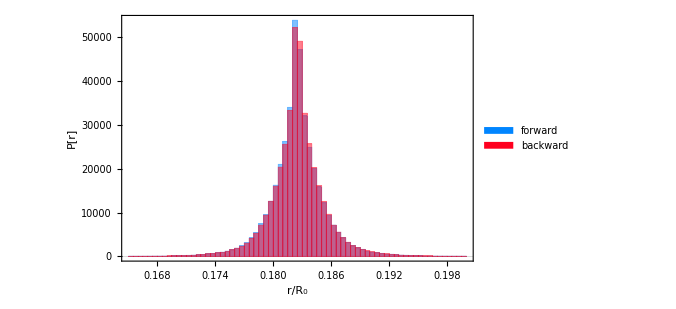

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["forward",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["backward",size2,FontFamily->"Times New Roman"]}}];fig16c=Histogram[Table[√((kz[[i]]-1)^2+kperp[[i]]^2)//Flatten,{i,1,2}],{0.06,0.3,0.003},PlotTheme->"Scientific",FrameLabel->{"r/R_0","P[r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.58],Hue[.98]},ChartLegends->Placed[legend,{0.8,0.8}]]
fig16d=Histogram[Table[√((kz[[i]]-1)^2+kperp[[i]]^2)//Flatten,{i,3,4}],{0.165,0.2,0.0005},PlotTheme->"Scientific",FrameLabel->{"r/R_0","P[r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.58],Hue[.98]},ChartLegends->Placed[legend,{0.8,0.8}]]
```

```mathematica
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(-t_0,t_0+t) - backward",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(0,t)   - backward   ",size2,FontFamily->"Times New Roman"]},{Graphics[{Red,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(t_0,t_0+t) - forward  ",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(0,t)   - forward     ",size2,FontFamily->"Times New Roman"]},{Graphics[{},ImageSize->size1],Style["t_0 = 50                    ",size2,FontFamily->"Times New Roman"]}}];i=1;tbase=1000;fig16e=ListLinePlot[{Table[{τ dt[[1]],10^6 Vcorff⟦1,tbase+1,tbase+τ⟧},{τ,-0tbase,Nt[[1]]-tbase,1}],Table[{τ dt[[1]],10^6 Vcorff⟦1,1,τ⟧},{τ,-0tbase,Nt[[1]]-tbase,1}],Table[{τ dt[[2]],10^6 Vcorff⟦2,tbase+1,tbase+τ⟧},{τ,-0tbase,Nt[[2]]-tbase,1}],Table[{τ dt[[2]],10^6 Vcorff⟦2,1,τ⟧},{τ,-0tbase,Nt[[2]]-tbase,1}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L [10^6v_th^2]"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[legend,{0.78,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Export[expfoto<>"fig_16_a.eps",fig16a]
Export[expfoto<>"fig_16_b.eps",fig16b]
Export[expfoto<>"fig_16_c.eps",fig16c]
Export[expfoto<>"fig_16_d.eps",fig16d]
Export[expfoto<>"fig_16_e.eps",fig16e]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_16_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_16_b.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_16_c.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_16_d.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_16_e.eps

```mathematica
(*SIngle neoclassical*)
```

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_d; λ = 0.3",size2,FontFamily->"Times New Roman"]},{Graphics[{Red,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_L; λ = 0.3",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_d; λ = 0.8",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Dashed,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["D_L; λ = 0.8",size2,FontFamily->"Times New Roman"]}}];i=1;
fig17a=ListLinePlot[{DQ1[[i]],Transpose[{t⟦1⟧,vth⟦1⟧^2 Λ.Vcorff⟦i,1⟧}],DQ1[[i+1]],Transpose[{t⟦1⟧,vth⟦1⟧^2 Λ.Vcorff⟦i+1,1⟧}]},PlotRange->{All,All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","D [m^2/s]"},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},PlotLegends->Placed[legend,{0.8,0.8}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
{size1,size2}={15,15};i=1;
legend=Grid[{{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->size1],Style["t = t_max; λ = 0.3",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->size1],Style["t = t_max; λ = 0.8",size2,FontFamily->"Times New Roman"]},{Graphics[{Black,Disk[{0,0},0.1]},ImageSize->size1],Style["t = t_0;     ",size2,FontFamily->"Times New Roman"]}}];fig17b=ListPlot[{Transpose[{kz[[i+1]]//Flatten,kperp[[i+1]]//Flatten}],Transpose[{kz[[i]]//Flatten,kperp[[i]]//Flatten}],{{kx[[i,1]],ky[[i,1]]}}},PlotRange->{{0.7,1.3},{-0.3,0.3}},PlotTheme->"Scientific",FrameLabel->{"R/R_0","Z/R_0"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,PlotStyle->{Blue,Red,{Black,PointSize[.02]}},AspectRatio->Full,PlotLegends->Placed[legend,{0.85,0.08}]]
```

```mathematica
{size1,size2}={15,18};legend=Grid[{{Graphics[{Hue[.98],Rectangle[{0,0}]},ImageSize->size1],Style["λ=0.3",size2,FontFamily->"Times New Roman"]},{Graphics[{Hue[.58],Rectangle[{0,0}]},ImageSize->size1],Style["λ=0.8",size2,FontFamily->"Times New Roman"]}}];fig17c=Histogram[{√((kz-1)^2+kperp^2)[[i]],√((kz-1)^2+kperp^2)[[i+1]]},{0.005},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"r/R_0","P[r]"},LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500,ChartStyle->{Hue[.98],Hue[.58]},ChartLegends->Placed[legend,{0.9,0.9}],AspectRatio->Full]
legend=Grid[{{Graphics[{Red,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(t_0,t_0+t)",size2,FontFamily->"Times New Roman"]},{Graphics[{Blue,Thick,Line[{{0,0},{2,0}}]},ImageSize->size1],Style["L(0,t)       ",size2,FontFamily->"Times New Roman"]},{Graphics[{},ImageSize->size1],Style["λ=0.3       ",size2,FontFamily->"Times New Roman"]}}];
tbase=180;fig17d=ListLinePlot[{Table[{τ dt[[1]],10^6 Vcorff⟦i,tbase+1,tbase+τ⟧},{τ,1,Nt[[i]]-tbase,1}],Table[{τ dt[[1]],10^6 Vcorff⟦i,1,τ⟧},{τ,1,Nt[[i]]-tbase,1}]},PlotRange->{{0,15},All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L [10^-6v_th^2]"},PlotStyle->{Red,{Blue,Dashed},Blue,{Red,Dashed}},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
base=60;fig17e=ListLinePlot[{Table[{τ dt[[1]],10^6 Vcorff⟦i+1,tbase+1,tbase+τ⟧},{τ,1,Nt[[i]]-tbase,1}],Table[{τ dt[[1]],10^6 Vcorff⟦i+1,1,τ⟧},{τ,1,Nt[[i]]-tbase,1}]},PlotRange->{{0,15},All},PlotTheme->"Scientific",FrameLabel->{"t[R_0/v_th]","L [10^-6v_th^2]"},PlotStyle->{Red,{Blue,Dashed},Blue,{Red,Dashed}},PlotLegends->Placed[legend,{0.8,0.7}],LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Luri=Table[{tbase1 dt[[1]],(tbase1+δt)dt[[1]],10^6 Vcorff⟦ja,tbase1,tbase1+δt⟧},{ja,2},{tbase1,1,Nt[[1]]/3},{δt,-tbase1+1,Nt⟦1⟧/3+1-tbase1}];
```

```mathematica
Luri=ArrayReshape[Luri,{nsim2,Dimensions[Luri][[2]]Dimensions[Luri][[3]],3}]//N;
```

```mathematica
fig17f=ListDensityPlot[Luri[[1]],PlotRange->All,PlotTheme->"Scientific",PlotRange->All,FrameLabel->{"t[R_0/v_th]","t'[R_0/v_th]","L(t,t')[10^-6v_th^2]"},ColorFunction->"TemperatureMap",PlotLegends->Automatic,LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
fig17g=ListDensityPlot[Luri[[2]],PlotRange->All,PlotTheme->"Scientific",PlotRange->All,FrameLabel->{"t[R_0/v_th]","t'[R_0/v_th]","L(t,t')[10^-6v_th^2]"},ColorFunction->"TemperatureMap",PlotLegends->Automatic,LabelStyle->{Black,Bold,18,FontFamily->"Times New Roman"},ImageSize->500]
```

```mathematica
Export[expfoto<>"fig_17_a.eps",fig17a]
Export[expfoto<>"fig_17_b.eps",fig17b,"AllowRasterization"->True]
Export[expfoto<>"fig_17_c.eps",fig17c]
Export[expfoto<>"fig_17_d.eps",fig17d]
Export[expfoto<>"fig_17_e.eps",fig17e]
Export[expfoto<>"fig_17_f.eps",fig17f,"AllowRasterization"->True]
Export[expfoto<>"fig_17_g.eps",fig17g,"AllowRasterization"->True]
```

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_a.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_b.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_c.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_d.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_e.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_f.eps

F:\5_Plasma\2_Present\4_Lagrangian_features\Arxiv\fig_17_g.eps

```mathematica
Export[expfoto<>"fig_17_f.eps",fig17f,"AllowRasterization"->True,ImageSize->500,ImageResize->500]
```

```mathematica
fact=1.0;neo=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,1,2}]/a0[[1]]/fact//Flatten;
coll=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,3,4}]/a0[[1]]/fact//Flatten;
turb=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,5,6}]/a0[[1]]/fact//Flatten;
full=Table[Sqrt[(kz[[as]]-1)^2+kperp[[as]]^2],{as,7,8}]/a0[[1]]/fact//Flatten;
neo=neo-Mean[neo];
coll=coll-Mean[coll];
turb=turb-Mean[turb];
full=full-Mean[full];
```

```mathematica
legend=Grid[{{Graphics[{Gray,Disk[{0,0},0.1]},ImageSize->15],Style["neo",15]},{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->15],Style["coll",15]},{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->15],Style["turb",15]},{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->15],Style["full",15]}}];histo=Histogram[{neo,coll,turb,full},{0.01},PlotRange->All,ScalingFunctions->"Log",PlotTheme->"Scientific",LabelStyle->{Black,Bold,18},ImageSize->500,FrameLabel->{"r/a","P"},ChartStyle->{Gray,Green,Blue,Red},ChartLegends->Placed[legend,{0.8,0.8}]]
```

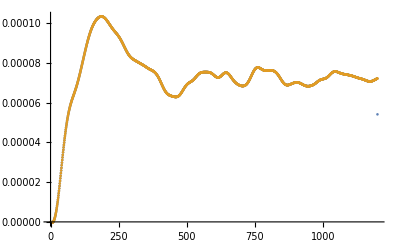
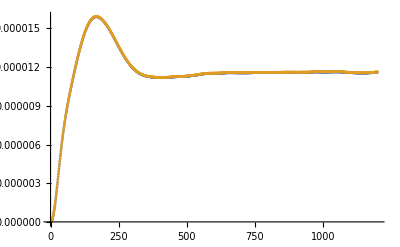

```mathematica
i=1;{ListPlot[{Λ.VQ1⟦i,All,2⟧,rhoi[[i]](𝓆1[[i]]-𝓆1[[i,1]])}],ListPlot[{Λ.DQ1[[i,All,2]],1/2 rhoi[[i]]^2(𝓆2[[i]]-𝓆1[[i]]^2)},PlotRange->All]}
```

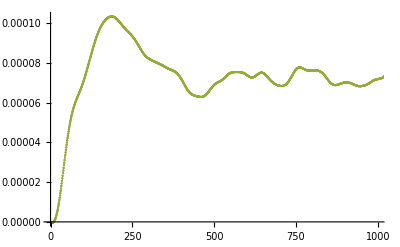
{-Graphics-,-Graphics-}

```mathematica
i=1;{ListPlot[{Λ.(vth⟦i⟧ Mean[Mean[VT⟦i⟧+V0⟦i⟧]]),Λ.VQ1⟦i,All,2⟧,rhoi⟦1⟧ (𝓆1⟦i⟧-𝓆1⟦i,1⟧)},PlotRange->{{0,999},Automatic}],ListPlot[{Λ.(vth⟦i⟧ Mean[Mean[VT⟦i⟧+V0⟦i⟧]])-Λ.VQ1⟦i,All,2⟧},PlotRange->{{0,999},Automatic}]}
```

```mathematica
i=2;ListLinePlot[{Λ.Mean[Mean[vth⟦i⟧ V0⟦i⟧]],Λ.Mean[Mean[vth⟦i⟧ VT⟦i⟧]],vth⟦i⟧ Λ.Mean[Mean[V0⟦i⟧+VT⟦i⟧]],rhoi⟦1⟧ (Mean[Mean[Q1⟦i⟧]]-Mean[Mean[Q1⟦i⟧]][[1]])},PlotStyle->{Red,Blue,Green,Orange},PlotLegends->Placed[{"Neo","Turb","full","real"},{1.,.6}],PlotRange->All,ImageSize->400]
```

$Aborted[]

```mathematica
Monitor[For[Simulation=1,Simulation≤17,Simulation++,folder=StringDrop[NotebookDirectory[],-12]<>"data/Sim_";
If[Simulation<10,folder=folder<>"0"<>ToString[Simulation]<>"/";,folder=folder<>ToString[Simulation]<>"/";];Subscript[fig, Simulation,1]=Import[folder<>"/fig_1_a.png"];Subscript[fig, Simulation,2]=Import[folder<>"/fig_1_b.png"];Subscript[fig, Simulation,3]=Import[folder<>"/fig_2_a.png"];Subscript[fig, Simulation,4]=Import[folder<>"/fig_2_b.png"];For[as=1,as≤nsim2,as++,Subscript[fig, Simulation,4+as]=Import[folder<>"/fig_3_"<>ToString[as]<>".png"]];],Simulation]
```

```mathematica
Subscript[fig, 11,4]
```

-Graphics-

```mathematica
Subscript[fig, 5,4]
```

-Graphics-

```mathematica
"home/dragos.palade/Work/FAST/01_02_2026/data/Sim_01"
```

Import::nffil: File /home/dragos.palade/Work/FAST/01_02_2026/data/Sim_1/fig_1_a.png not found during Import.

Import::nffil: File /home/dragos.palade/Work/FAST/01_02_2026/data/Sim_1/fig_1_b.png not found during Import.

Import::nffil: File /home/dragos.palade/Work/FAST/01_02_2026/data/Sim_1/fig_2_a.png not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Import::noelem: The Import element "…" is not present when importing as PNG.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Import::noelem: The Import element "…" is not present when importing as PNG.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Import::noelem: The Import element "…" is not present when importing as PNG.

General::stop: Further output of Import::noelem will be suppressed during this calculation.

```mathematica
folder
```

/home/dragos.palade/Work/FAST/01_02_2026/data/Sim_17/

```mathematica
folder
```

/home/dragos.palade/Work/FAST/01_02_2026/data/Sim_07/

```mathematica
sdsd={"Ts", "As", "Zs", "X0", "k0i", "tauc", "lbalonz", "lambdaz", "lambday", "lambdax", "Phi",
 "Omgtprim", "Omgt0", "safe3", "safe1", "B0"}
Table[Position[names,sdsd[[o]]][[1,1]],{o,Length[sdsd]}]
```

{Tw,Aw,Zw,X0,k0i,tauc,lbalonz,lambdaz,lambday,lambdax,Phi,Omgtprim,Omgt0,safe3,safe1,B0}

```mathematica
{Tw,Aw,Zw,X0,k0i,tauc,lbalonz,lambdaz,lambday,lambdax,Phi,Omgtprim,Omgt0,safe3, safe1, B0}
```

```mathematica
pozvar=Position[HeavisideTheta[Abs[pars⟦1⟧-pars⟦2⟧]],1]⟦1,1⟧;
cine=names⟦pozvar-len⟧;
cat=pars⟦All,pozvar⟧;
cc={ListPlot[Transpose[{cat,VQas}],PlotTheme->"Scientific",FrameLabel->{cine,"V[m^2/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotMarkers->Automatic,PlotRange->All],ListPlot[Transpose[{cat,DQas}],PlotTheme->"Scientific",FrameLabel->{cine,"D[m^2/s]"},LabelStyle->{Black,Bold,18},ImageSize->500,Joined->True,PlotMarkers->Automatic,PlotRange->All]}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

«18 more identical outputs»